## Импорт библиотек

```mathematica
If[$FrontEnd =!= Null, AppendTo[$Path, FileNameJoin[{NotebookDirectory[], #}]]&/@{"../../lib/mathematica","../lib"}];

(Once@Get[#] &) /@ { "Formal.m", "Features.m", "Ricci_grav.m", "aux-2-grav-generic.m" };
```

SetDelayed::write: Tag Div in Div[V_] is Protected.

```mathematica
EnableFeature[{Formatter[DD],Formatter[Tensor]}];
```

## Решения

### Вспомогательное

```mathematica
GGM={{-1,0,0,0},{0,1,0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[u]^2}};
GGPW={{-1+Rs/r,-√(Rs/r),0,0},{-√(Rs/r),1,0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[u]^2}};
GGSW={{-1+Rs/r,0,0,0},{0,r/(r-Rs),0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[u]^2}};
```

```mathematica
fs=Tensor[f,0,0][];
```

```mathematica
tmu=TensorContr[tm];
```

```mathematica
ta=Tensor[a,0,1];
te=Tensor[e,0,1];
tb=Tensor[b,1,0];
tF=Tensor[F,0,2];
tFu=Tensor[F,2,0];
```

```mathematica
tdR=Tensor[δR,0,2];
tdΓ=Tensor[δΓ,1,2];
```

```mathematica
luu={Yl'[u]->Yv[u],Yv'[u]->-l (1+l) Yl[u]-Cot[u] Yv[u],Yt'[u]->-2 Cot[u] Yt[u]-(-1+l) (2+l) Yv[u],Yl''[u]->-l (1+l) Yl[u]-Cot[u] Yv[u],Yv''[u]->l (1+l) Cot[u] Yl[u]+(-l (1+l)+Cot[u]^2+Csc[u]^2) Yv[u],Yt''[u]->l (-2-l+2 l^2+l^3) Yl[u]+2 (2+Cos[2 u]) Csc[u]^2 Yt[u]+3 (-2+l+l^2) Cot[u] Yv[u]};
```

```mathematica
SetAttributes[intro,HoldAll];
SetAttributes[rewrite,HoldAll];
SetAttributes[rewriteT,HoldAll];
```

```mathematica
rewrite[def_][eq_]:=eq//.intro[def];
rewriteT[def_][eq_]:=rewrite[def][eq]//Tensorify//TensorBeautify;
```

#### Преобразование метрики Шварцшильда к метрике Пенлеве

```mathematica
GGSW0=DiagonalMatrix[{-P[r],Q[r],r^2,r^2 Sin[u]^2}]
GGSP0=-Make4Metrics[DiagonalMatrix[{B[r]^-2,r^2,r^2 Sin[u]^2}], {B[r]V[r],0,0}]
```

{{-P[r],0,0,0},{0,Q[r],0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[u]^2}}

{{-1+V[r]^2,-V[r]/B[r],0,0},{-V[r]/B[r],1/B[r]^2,0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[u]^2}}

```mathematica
coordsSW0={ct+W[r],r,u,w};
coordsPW0={ct,r,u,w};
transSW2PW0=Table[D[coordsSW0[[i]],coordsPW0[[j]]],{i,1,4},{j,1,4}]/.W'[r]->w[r]
```

{{1,w[r],0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
GGSP1=Table[Sum[transSW2PW0[[ii,i]]transSW2PW0[[jj,j]]GGSW0[[ii,jj]],{ii,1,4},{jj,1,4}],{i,1,4},{j,1,4}]//S
```

{{-P[r],-P[r] w[r],0,0},{-P[r] w[r],Q[r]-P[r] w[r]^2,0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[u]^2}}

```mathematica
GGSPd=GGSP0-GGSP1//Flatten//Cases[Except[0]]//DeleteDuplicates//S
```

{-1+P[r]+V[r]^2,-V[r]/B[r]+P[r] w[r],1/B[r]^2-Q[r]+P[r] w[r]^2}

```mathematica
GGSPt=Solve[GGSPd==0//Thread,{V[r],B[r],w[r]}]
```

{{V[r]→(√(-(-1+P[r]) Q[r]))/(√Q[r]),B[r]→-1/(√P[r] √Q[r]),w[r]→-(√(Q[r]-P[r] Q[r]))/(√P[r])},{V[r]→-(√(-(-1+P[r]) Q[r]))/(√Q[r]),B[r]→-1/(√P[r] √Q[r]),w[r]→(√(Q[r]-P[r] Q[r]))/(√P[r])},{V[r]→-(√(-(-1+P[r]) Q[r]))/(√Q[r]),B[r]→1/(√P[r] √Q[r]),w[r]→-(√(Q[r]-P[r] Q[r]))/(√P[r])},{V[r]→(√(-(-1+P[r]) Q[r]))/(√Q[r]),B[r]→1/(√P[r] √Q[r]),w[r]→(√(Q[r]-P[r] Q[r]))/(√P[r])}}

```mathematica
GGSW0
GGSW
```

{{-P[r],0,0,0},{0,Q[r],0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[u]^2}}

{{-1+Rs/r,0,0,0},{0,r/(r-Rs),0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[u]^2}}

```mathematica
GGSPtn=S@(GGSPt/.{P[r]->-GGSW[[1,1]],Q[r]->GGSW[[2,2]]})//.{√a_ √b_:>√(a b),√a_/√b_:>√(a / b)}//FullSimplify//PowerExpand//Last
```

{V[r]→(√Rs)/(√r),B[r]→1,w[r]→(√r √Rs)/(r-Rs)}

```mathematica
GGSP0/.GGSPtn//S
GGPW
```

{{-1+Rs/r,-(√Rs)/(√r),0,0},{-(√Rs)/(√r),1,0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[u]^2}}

{{-1+Rs/r,-√(Rs/r),0,0},{-√(Rs/r),1,0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[u]^2}}

```mathematica
SW2PW=transSW2PW0/.Last@GGSPtn
```

{{1,(√r √Rs)/(r-Rs),0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

#### Решения Уилера

```mathematica
ylm[u_,w_]:=(-1)^m ⅇ^(ⅈ m w)LegendreP[l,m,Cos[u]];
```

Решения без преобразования координат

```mathematica
hwO=Module[{hwt},
hwt[0,0]=hwt[0,1]=hwt[1,1]=0;
hwt[0,2]=-h0[r] 1/Sin[u] D[ylm[u,w],w];
hwt[0,3]=h0[r]Sin[u]D[ylm[u,w],u];
hwt[1,2]=-h1[r] 1/Sin[u] D[ylm[u,w],w];
hwt[1,3]=h1[r]Sin[u]D[ylm[u,w],u];
hwt[2,2]=h2[r](1/Sin[u] D[ylm[u,w],u,w]-Cos[u]/Sin[u]^2 D[ylm[u,w],w]);
hwt[2,3]=1/2 h2[r](1/Sin[u] D[ylm[u,w],w,w]+Cos[u]D[ylm[u,w],u]-Sin[u]D[ylm[u,w],u,u]);
hwt[3,3]=-h2[r](Sin[u]D[ylm[u,w],u,w]+Cos[u]D[ylm[u,w],w]);
hwt[i_,j_]:=hwt[j,i]/;i>j;
Array[hwt,{4,4},{0,0}] ⅇ^(-ⅈ ω ct)
];
```

```mathematica
hwE=Module[{hwt},
hwt[0,0]=(1-Rs/r)H0[r]ylm[u,w];
hwt[0,1]=H1[r]ylm[u,w];
hwt[0,2]=h0[r]D[ylm[u,w],u];
hwt[0,3]=h0[r]D[ylm[u,w],w];
hwt[1,1]=(1-Rs/r)^-1 H2[r]ylm[u,w];
hwt[1,2]=h1[r]D[ylm[u,w],u];
hwt[1,3]=h1[r]D[ylm[u,w],w];
hwt[2,2]=r^2(Kk[r]ylm[u,w]+Gg[r]D[ylm[u,w],u,u]);
hwt[2,3]=r^2 Gg[r](D[ylm[u,w],u,w]-Cos[u]/Sin[u]D[ylm[u,w],w]);
hwt[3,3]=r^2(Kk[r] Sin[u]^2 ylm[u,w]+Gg[r](D[ylm[u,w],w,w]+Sin[u]Cos[u]D[ylm[u,w],u]));
hwt[i_,j_]:=hwt[j,i]/;i>j;
Array[hwt,{4,4},{0,0}] ⅇ^(-ⅈ ω ct)
];
```

Решения в канонической форме с m = 0

```mathematica
hwSO=Module[{hwt},
hwt[i_,j_]:=0;
hwt[0,3]=h0[r];
hwt[1,3]=h1[r];
hwt[i_,j_]:=hwt[j,i]/;i>j;
Array[hwt,{4,4},{0,0}] ⅇ^(-ⅈ ω ct)Sin[u]D[LegendreP[l,Cos[u]],u]
];
```

```mathematica
hwSE=Module[{hwt},
hwt[i_,j_]:=0;
hwt[0,0]=H0[r](1-Rs/r);
hwt[0,1]=H1[r];
hwt[1,1]=H2[r](1-Rs/r)^-1;
hwt[2,2]=r^2 Kk[r];
hwt[3,3]=r^2 Sin[u]^2 Kk[r];
hwt[i_,j_]:=hwt[j,i]/;i>j;
Array[hwt,{4,4},{0,0}] ⅇ^(-ⅈ ω ct)LegendreP[l,Cos[u]]
];
```

Выборка разделяемых компонентов уравнений для простоты исследования

```mathematica
relTEqs[h_]:=(((Part[h,##]&) @@ #&)/@{{1,1},{1,2},{1,3},{1,4},{2,2},{2,3},{2,4}});
```

```mathematica
remU[e_]:=(e/.{_[u]:>1, _[_ u]:>1})
```

#### Функции

```mathematica
evalTijS[expr_,L_,U_]:=expr/.l->L/.u->U/.ct->0
evalTij[expr_,L_,U_]:=evalTijS[expr,L,U]//FunctionExpand//ExpandAll//ComplexExpand//S
```

```mathematica
eTij[Tij_]:=Tij[[1,1]]
uTij[Tij_]:=Tij[[1,2;;]]
dTij[Tij_]:={eTij@Tij, uTij@Tij}
```

### Скалярное поле в метрике Пенлеве

```mathematica
Ricci[{ct,r,u,w},GGPW];
```

```mathematica
Ls = SSum[1/2tmu[i,j]ð[fs,Cov[i]]ð[fs,Cov[j]],i,j]
```

S_i S_j(1/2 (f_^)_(;i) (f_^)_(;j) γ_^ij)

```mathematica
Lsvar = SSum[-tmu[i,j]ð[fs,Cov[i],Cov[j]],i,j]
```

S_i S_j(-(f_^)_(;ij) γ_^ij)

#### Напрямую через Eq[L]

```mathematica
Lsns=gd Ls//.SSum2SumRules[{#,0,3}&]/.tmu->hh//S
```

1/2 (-r^2 (f_^)_(;0)^2-2 r^2 √(Rs/r) (f_^)_(;0) (f_^)_(;1)+r (r-Rs) (f_^)_(;1)^2+(f_^)_(;2)^2+Csc[u]^2 (f_^)_(;3)^2) Sin[u]

```mathematica
Lsn=EvaluateAt[Lsns,fs->f[ct,r,u]]//S
```

1/2 Sin[u] ((f^(0,0,1)[ct,r,u])^2+r ((r-Rs) (f^(0,1,0)[ct,r,u])^2-2 r √(Rs/r) f^(0,1,0)[ct,r,u] f^(1,0,0)[ct,r,u]-r (f^(1,0,0)[ct,r,u])^2))

```mathematica
Vars=Eq[Lsn,f[ct,r,u]]//S
```

-Cos[u] f^(0,0,1)[ct,r,u]-1/2 Sin[u] (2 f^(0,0,2)[ct,r,u]+(4 r-2 Rs) f^(0,1,0)[ct,r,u]+r (2 (r-Rs) f^(0,2,0)[ct,r,u]-3 √(Rs/r) f^(1,0,0)[ct,r,u]-2 r (2 √(Rs/r) f^(1,1,0)[ct,r,u]+f^(2,0,0)[ct,r,u])))

```mathematica
eqfs=(Vars/.f->Function[{ct,r,u},Yl[u] ⅇ^(ⅈ ct)ww[r]])/(1/2 ⅇ^(ⅈ ct) Sin[u] Yl[u])//.luu//S
```

(2 l+2 l^2+r (-2 r+3 ⅈ √(Rs/r))) ww[r]+2 ((-2 r+Rs+2 ⅈ r^2 √(Rs/r)) ww'[r]+r (-r+Rs) ww''[r])

#### Через тензорификацию

```mathematica
Lsvarn=(Lsvar//CovExpand//Tensorify//TensorBeautify)//.SSum2SumRules[{#,0,3}&]/.TensorChristoffel[]->cs2/.tmu->hh/.ð[fs,3,3]->0/.ð[fs,1,0]->ð[fs,0,1]//FullSimplify
```

(3 r √(Rs/r) (f_^)_(,0)+2 ((-2 r+Rs) (f_^)_(,1)+r (r (f_^)_(,00)+2 r √(Rs/r) (f_^)_(,01)+(-r+Rs) (f_^)_(,11)))-2 (Cot[u] (f_^)_(,2)+(f_^)_(,22)))/(2 r^2)

```mathematica
eqfs=EvaluateAt[Lsvarn,fs->Yl[u] ww[r] ⅇ^(ⅈ ct)]2 r^2/ⅇ^(ⅈ ct)/Yl[u]//.luu//S
```

(2 l+2 l^2+r (-2 r+3 ⅈ √(Rs/r))) ww[r]+2 ((-2 r+Rs+2 ⅈ r^2 √(Rs/r)) ww'[r]+r (-r+Rs) ww''[r])

#### Преобразование метрик

```mathematica
tmp=EvaluateAt[Lsvarn,fs->Yl[u] ww[r] ⅇ^(ⅈ f[ct,r])]2 r^2/Yl[u]/ⅇ^(ⅈ f[ct,r])//.luu/.
f->Function[{ct,r},f0[ct+2 √r √(Rs/r) (√r-√Rs ArcTanh[(√r)/(√Rs)])]]/.
f0->Function[{s},s+ⅈ ⅇ^(-ⅈ s) C[1]+C[2]]/.C[1]->0//S//FullSimplify
```

-(2 ((-l (1+l) r+r^3+l (1+l) Rs) ww[r]+(2 r^2-3 r Rs+Rs^2) ww'[r]+r (r-Rs)^2 ww''[r]))/(r-Rs)

```mathematica
eqfsSW
```

-(2 ((r^3+l (-r+Rs)+l^2 (-r+Rs)) ww[r]+(r-Rs) ((2 r-Rs) ww'[r]+r (r-Rs) ww''[r])))/(r-Rs)

```mathematica
Coefficient[eqfsSW,ww'[r]]//S
Coefficient[tmp,ww'[r]]//S
```

-4 r+2 Rs

-4 r+2 Rs

```mathematica
DSolve[Coefficient[eqfsSW,ww'[r]]==Coefficient[tmp,ww'[r]],f[ct,r],{ct,r}]//FullSimplify
```

{{f[ct,r]→C[1][ct+2 √r √(Rs/r) (√r-√Rs ArcTanh[(√r)/(√Rs)])]}}

```mathematica
Coefficient[eqfsSW,ww[r]]//S
Coefficient[tmp,ww[r]]//S
```

-(2 (r^3+l (-r+Rs)+l^2 (-r+Rs)))/(r-Rs)

1/(r-Rs)2 (l (r-Rs)+l^2 (r-Rs)+r^3 (-1-ⅇ^(-2 ⅈ (ct+2 r √(Rs/r)-√r √Rs √(Rs/r) ArcTanh[(√r)/(√Rs)])) C[1] (ⅇ^(ⅈ (ct+2 r √(Rs/r)))+ⅇ^(2 ⅈ √r √Rs √(Rs/r) ArcTanh[(√r)/(√Rs)]) C[1])))

```mathematica
(Coefficient[eqfsSW,ww[r]]-Coefficient[tmp,ww[r]])/2 r^-3//FullSimplify//Numerator
```

-1+f0'[ct+2 √r √(Rs/r) (√r-√Rs ArcTanh[(√r)/(√Rs)])]^2-ⅈ f0''[ct+2 √r √(Rs/r) (√r-√Rs ArcTanh[(√r)/(√Rs)])]

```mathematica
DSolve[-1+f0'[s]-ⅈ f0''[s]==0,f0[s],s]//S
```

{{f0[s]→s+ⅈ ⅇ^(-ⅈ s) C[1]+C[2]}}

```mathematica
(Coefficient[eqfsSW,ww[r]]-Coefficient[tmp,ww[r]])//S
```

(2 ⅇ^(-2 ⅈ (ct+2 r √(Rs/r)-√r √Rs √(Rs/r) ArcTanh[(√r)/(√Rs)])) r^3 C[1] (ⅇ^(ⅈ (ct+2 r √(Rs/r)))+ⅇ^(2 ⅈ √r √Rs √(Rs/r) ArcTanh[(√r)/(√Rs)]) C[1]))/(r-Rs)

```mathematica
-ctpw + f0[ct+2 √r √(Rs/r) (√r-√Rs ArcTanh[(√r)/(√Rs)])]/.f0->Function[{s},s+ⅈ ⅇ^(-ⅈ s) C[1]+C[2]]/.C[1]->0/.ct->ctsw//FullSimplify//PowerExpand
```

-ctpw+ctsw+2 √Rs (√r-√Rs ArcTanh[(√r)/(√Rs)])+C[2]

### Скалярное поле в метрике Шварцшильда

```mathematica
Ricci[{ct,r,u,w},GGSW];
```

```mathematica
Ls = SSum[1/2tmu[i,j]ð[fs,Cov[i]]ð[fs,Cov[j]],i,j]
```

S_i S_j(1/2 (f_^)_(;i) (f_^)_(;j) γ_^ij)

```mathematica
Lsvar = SSum[-tmu[i,j]ð[fs,Cov[i],Cov[j]],i,j]
```

S_i S_j(-(f_^)_(;ij) γ_^ij)

#### Напрямую через Eq[L]

```mathematica
Lsns=gd Ls//.SSum2SumRules[{#,0,3}&]/.tmu->hh//S
```

((-r^3 (f_^)_(;0)^2+(r-Rs) (r (r-Rs) (f_^)_(;1)^2+(f_^)_(;2)^2+Csc[u]^2 (f_^)_(;3)^2)) Sin[u])/(2 (r-Rs))

```mathematica
Lsn=EvaluateAt[Lsns,fs->f[ct,r,u]]//S
```

(Sin[u] ((r-Rs) ((f^(0,0,1)[ct,r,u])^2+r (r-Rs) (f^(0,1,0)[ct,r,u])^2)-r^3 (f^(1,0,0)[ct,r,u])^2))/(2 (r-Rs))

```mathematica
Vars=Eq[Lsn,f[ct,r,u]]//S
```

-Cos[u] f^(0,0,1)[ct,r,u]+Sin[u] (-f^(0,0,2)[ct,r,u]+(-2 r+Rs) f^(0,1,0)[ct,r,u]-(r ((r-Rs)^2 f^(0,2,0)[ct,r,u]-r^2 f^(2,0,0)[ct,r,u]))/(r-Rs))

```mathematica
eqfsSW=(Vars/.f->Function[{ct,r,u},Yl[u] ⅇ^(ⅈ ct)ww[r]])/(1/2 ⅇ^(ⅈ ct) Sin[u] Yl[u])//.luu//S
```

-(2 ((r^3+l (-r+Rs)+l^2 (-r+Rs)) ww[r]+(r-Rs) ((2 r-Rs) ww'[r]+r (r-Rs) ww''[r])))/(r-Rs)

#### Через тензорификацию

```mathematica
Lsvarn=(Lsvar//CovExpand//Tensorify//TensorBeautify)//.SSum2SumRules[{#,0,3}&]/.TensorChristoffel[]->cs2/.tmu->hh/.ð[fs,3,3]->0/.ð[fs,1,0]->ð[fs,0,1]//FullSimplify
```

(-(2 r^2-3 r Rs+Rs^2) (f_^)_(,1)+(-r+Rs) Cot[u] (f_^)_(,2)+r^3 (f_^)_(,00)-r (r-Rs)^2 (f_^)_(,11)+(-r+Rs) (f_^)_(,22))/(r^2 (r-Rs))

```mathematica
eqfsSW=EvaluateAt[Lsvarn,fs->Yl[u] ww[r] ⅇ^(ⅈ ct)]2 r^2/ⅇ^(ⅈ ct)/Yl[u]//.luu//S
```

-(2 ((r^3+l (-r+Rs)+l^2 (-r+Rs)) ww[r]+(r-Rs) ((2 r-Rs) ww'[r]+r (r-Rs) ww''[r])))/(r-Rs)

#### Преобразование метрик

```mathematica
tmp=EvaluateAt[Lsvarn,fs->Yl[u] ww[r] ⅇ^(ⅈ f[ct,r])]2 r^2/Yl[u]/ⅇ^(ⅈ f[ct,r])//.luu/.
f->Function[{ct,r},-2 √r √(Rs/r) (√r-√Rs ArcTanh[(√r)/(√Rs)])+f1[ct]]/.
f1->Function[{ct},-ct+C[2]-ⅈ Log[ⅇ^(2 ⅈ ct)+ⅇ^(2 C[1])]]//S
```

(2 l+2 l^2+r (-2 r+3 ⅈ √(Rs/r))) ww[r]+2 ((-2 r+Rs+2 ⅈ r^2 √(Rs/r)) ww'[r]+r (-r+Rs) ww''[r])

```mathematica
eqfs
```

(2 l+2 l^2+r (-2 r+3 ⅈ √(Rs/r))) ww[r]+2 ((-2 r+Rs+2 ⅈ r^2 √(Rs/r)) ww'[r]+r (-r+Rs) ww''[r])

```mathematica
Coefficient[eqfs,ww'[r]]//S
Coefficient[tmp,ww'[r]]//S
```

2 (-2 r+Rs+2 ⅈ r^2 √(Rs/r))

2 (-2 r+Rs+2 ⅈ r^2 √(Rs/r))

```mathematica
DSolve[ Coefficient[eqfs,ww'[r]]==Coefficient[tmp,ww'[r]],f[ct,r],{ct,r}]//FullSimplify
```

{{f[ct,r]→-2 √r √(Rs/r) (√r-√Rs ArcTanh[(√r)/(√Rs)])+C[1][ct]}}

```mathematica
Coefficient[eqfs,ww[r]]//S
Coefficient[tmp,ww[r]]//S
```

2 l+2 l^2+r (-2 r+3 ⅈ √(Rs/r))

(2 l r+2 l^2 r-2 l Rs-2 l^2 Rs+2 r^2 Rs+3 ⅈ r^2 √(Rs/r)-3 ⅈ r Rs √(Rs/r)-2 r^3 f1'[ct]^2+2 ⅈ r^3 f1''[ct])/(r-Rs)

```mathematica
DSolve[Coefficient[eqfs,ww[r]]==Coefficient[tmp,ww[r]],f1[ct],ct]
```

{{f1[ct]→-ct+C[2]-ⅈ Log[ⅇ^(2 ⅈ ct)+ⅇ^(2 C[1])]}}

```mathematica
-ctct+-2 √r √(Rs/r) (√r-√Rs ArcTanh[(√r)/(√Rs)])+-ct+C[2]-ⅈ Log[ⅇ^(2 ⅈ ct)+ⅇ^(2 C[1])]//FullSimplify
```

-ct-ctct-2 √r √(Rs/r) (√r-√Rs ArcTanh[(√r)/(√Rs)])+C[2]-ⅈ Log[ⅇ^(2 ⅈ ct)+ⅇ^(2 C[1])]

### Скалярное поле в метрике Минковского

```mathematica
Ricci[{ct,r,u,w},GGM];
```

```mathematica
Ls = SSum[1/2tmu[i,j]ð[fs,Cov[i]]ð[fs,Cov[j]],i,j]
```

S_i S_j(1/2 (f_^)_(;i) (f_^)_(;j) γ_^ij)

```mathematica
Lsvar = SSum[-tmu[i,j]ð[fs,Cov[i],Cov[j]],i,j]
```

S_i S_j(-(f_^)_(;ij) γ_^ij)

```mathematica
Tij =Table[SSum[1/2ð[fs,k]ð[fs,l](tmu[i,k]tmu[j,l]-tmu[i,j]tmu[k,l]),k,l],{i,0,3},{j,0,3}];
```

#### Напрямую через Eq[L]

```mathematica
Lsns=gd Ls//.SSum2SumRules[{#,0,3}&]/.tmu->hh//S
```

1/2 (-r^2 (f_^)_(;0)^2+r^2 (f_^)_(;1)^2+(f_^)_(;2)^2+Csc[u]^2 (f_^)_(;3)^2) Sin[u]

```mathematica
Lsn=EvaluateAt[Lsns,fs->f[ct,r,u]]//S
```

1/2 Sin[u] ((f^(0,0,1)[ct,r,u])^2+r^2 ((f^(0,1,0)[ct,r,u])^2-(f^(1,0,0)[ct,r,u])^2))

```mathematica
Vars=Eq[Lsn,f[ct,r,u]]//S
```

-Cos[u] f^(0,0,1)[ct,r,u]-Sin[u] (f^(0,0,2)[ct,r,u]+r (2 f^(0,1,0)[ct,r,u]+r f^(0,2,0)[ct,r,u]-r f^(2,0,0)[ct,r,u]))

```mathematica
eqfsM=(Vars/.f->Function[{ct,r,u},Yl[u] ⅇ^(ⅈ ct)ww[r]])/(1/2 ⅇ^(ⅈ ct) Sin[u] Yl[u])//.luu//S
```

2 ((l+l^2-r^2) ww[r]-r (2 ww'[r]+r ww''[r]))

```mathematica
DSolve[eqfsM==0,ww[r],r]
```

{{ww[r]→C[1] SphericalBesselJ[l,r]+C[2] SphericalBesselY[l,r]}}

```mathematica
fslnM = { ww -> Function[{r}, SphericalHankelH1[l,r]] };
```

#### Тензор энергии-импульса

```mathematica
Tijs=Table[(gd Tij[[ii,jj]]//CovExpand)//.SSum2SumRules[{#,0,3}&]/.TensorChristoffel[]->cs2/.tmu->hh//S,{ii,1,4},{jj,1,4}];
```

```mathematica
Tijsr=(Tijs//ExpandAll)/.{(x:fs|ð[fs,_])(y:fs|ð[fs,_]):>1/2Re[x Conjugate[y]], (x:fs|ð[fs,_])^2:>1/2Re[x Conjugate[x]]};
```

```mathematica
Tijn=EvaluateAt[Tijs,fs:>f[ct,r,u]]//S;
```

```mathematica
Tijr=EvaluateAt[Tijsr,fs:>f[ct,r,u]]//S;
```

```mathematica
Tijr/.f->Function[{ct,r,u},LegendreP[l,Cos[u]] ⅇ^(ⅈ ct)SphericalHankelH1[l,r]]//S;
Tijrn=Simplify[%,Assumptions->((r|ct|u|LegendreP[a_,b__])∈Reals)&&(l∈Integers)];
```

```mathematica
{ee2,UU2}=evalTij[dTij@Tijrn,2,u]
```

{((1215+207 r^2+14 r^4+11 r^6+12 (81+9 r^2-2 r^4+r^6) Cos[2 u]+9 (45-3 r^2-6 r^4+r^6) Cos[4 u]) Sin[u])/(128 r^6),{-1/64 (1+3 Cos[2 u])^2 Sin[u],0,0}}

```mathematica
Row[{ParametricPlot3D[{r Cos[u],r Sin[u],10ee2//Evaluate},{r,0,7},{u,0,π},PlotRange->{Full,Full,{0,5}}]
ParametricPlot3D[{r Cos[u],r Sin[u],-60UU2[[1]]//Evaluate},{r,0,7},{u,0,π},PlotRange->{Full,Full,{0,5}}]}]
```

-Graphics3D- -Graphics3D-

### Векторное поле в метрике Шварцшильда

```mathematica
Ricci[{ct,r,u,w},GGSW];
```

```mathematica
intro[tF]:=tF[i_,k_]:>ð[ta[i],Cov[k]]-ð[ta[k],Cov[i]];
```

```mathematica
Ls = -SSum[1/4tmu[i,k]tmu[j,l]tF[i,j]tF[k,l],i,j,k,l]
```

-(S_i S_j S_k S_l(1/4 F_ij^ F_kl^ γ_^ik γ_^jl))

```mathematica
Lsa=Ls//rewriteT[tF]
```

S_i S_j S_k S_l(-1/4 (a_i^)_(;j) (a_k^)_(;l) γ_^ik γ_^jl+1/4 (a_j^)_(;i) (a_k^)_(;l) γ_^ik γ_^jl+1/4 (a_i^)_(;j) (a_l^)_(;k) γ_^ik γ_^jl-1/4 (a_j^)_(;i) (a_l^)_(;k) γ_^ik γ_^jl)

#### Напрямую через Eq[L]

```mathematica
Lsns=(gd Lsa//CovExpand)//.SSum2SumRules[{#,0,3}&]/.TensorChristoffel[]->cs2/.tmu->hh//S
```

1/(2 r^2 (r-Rs))(r^3 Csc[u] (a_0^)_(,3)^2-2 r^3 Csc[u] (a_0^)_(,3) (a_3^)_(,0)+(r^4 (r-Rs) (a_0^)_(,1)^2+r^3 (a_0^)_(,2)^2+2 r^4 (-r+Rs) (a_0^)_(,1) (a_1^)_(,0)+r^5 (a_1^)_(,0)^2-r^4 Rs (a_1^)_(,0)^2-r^3 (a_1^)_(,2)^2+2 r^2 Rs (a_1^)_(,2)^2-r Rs^2 (a_1^)_(,2)^2-r^3 Csc[u]^2 (a_1^)_(,3)^2+2 r^2 Rs Csc[u]^2 (a_1^)_(,3)^2-r Rs^2 Csc[u]^2 (a_1^)_(,3)^2-2 r^3 (a_0^)_(,2) (a_2^)_(,0)+r^3 (a_2^)_(,0)^2+2 r^3 (a_1^)_(,2) (a_2^)_(,1)-4 r^2 Rs (a_1^)_(,2) (a_2^)_(,1)+2 r Rs^2 (a_1^)_(,2) (a_2^)_(,1)-r^3 (a_2^)_(,1)^2+2 r^2 Rs (a_2^)_(,1)^2-r Rs^2 (a_2^)_(,1)^2-r Csc[u]^2 (a_2^)_(,3)^2+Rs Csc[u]^2 (a_2^)_(,3)^2+r^3 Csc[u]^2 (a_3^)_(,0)^2+2 r^3 Csc[u]^2 (a_1^)_(,3) (a_3^)_(,1)-4 r^2 Rs Csc[u]^2 (a_1^)_(,3) (a_3^)_(,1)+2 r Rs^2 Csc[u]^2 (a_1^)_(,3) (a_3^)_(,1)-r^3 Csc[u]^2 (a_3^)_(,1)^2+2 r^2 Rs Csc[u]^2 (a_3^)_(,1)^2-r Rs^2 Csc[u]^2 (a_3^)_(,1)^2+2 r Csc[u]^2 (a_2^)_(,3) (a_3^)_(,2)-2 Rs Csc[u]^2 (a_2^)_(,3) (a_3^)_(,2)-r Csc[u]^2 (a_3^)_(,2)^2+Rs Csc[u]^2 (a_3^)_(,2)^2) Sin[u])

```mathematica
Lsn=EvaluateAt[Lsns,ta[i_]:>{f0[ct,r,u],f1[ct,r,u],f2[ct,r,u],Sin[u]f3[ct,r,u]}[[i+1]]]//S
```

1/(2 r^2 (r-Rs))Sin[u] (r^3 (f0^(0,0,1)[ct,r,u])^2-r^3 (f1^(0,0,1)[ct,r,u])^2+2 r^2 Rs (f1^(0,0,1)[ct,r,u])^2-r Rs^2 (f1^(0,0,1)[ct,r,u])^2-r (Cot[u] f3[ct,r,u]+f3^(0,0,1)[ct,r,u])^2+Rs (Cot[u] f3[ct,r,u]+f3^(0,0,1)[ct,r,u])^2+r^4 (r-Rs) (f0^(0,1,0)[ct,r,u])^2+2 r^3 f1^(0,0,1)[ct,r,u] f2^(0,1,0)[ct,r,u]-4 r^2 Rs f1^(0,0,1)[ct,r,u] f2^(0,1,0)[ct,r,u]+2 r Rs^2 f1^(0,0,1)[ct,r,u] f2^(0,1,0)[ct,r,u]-r^3 (f2^(0,1,0)[ct,r,u])^2+2 r^2 Rs (f2^(0,1,0)[ct,r,u])^2-r Rs^2 (f2^(0,1,0)[ct,r,u])^2-r^3 (f3^(0,1,0)[ct,r,u])^2+2 r^2 Rs (f3^(0,1,0)[ct,r,u])^2-r Rs^2 (f3^(0,1,0)[ct,r,u])^2+2 r^4 (-r+Rs) f0^(0,1,0)[ct,r,u] f1^(1,0,0)[ct,r,u]+r^5 (f1^(1,0,0)[ct,r,u])^2-r^4 Rs (f1^(1,0,0)[ct,r,u])^2-2 r^3 f0^(0,0,1)[ct,r,u] f2^(1,0,0)[ct,r,u]+r^3 (f2^(1,0,0)[ct,r,u])^2+r^3 (f3^(1,0,0)[ct,r,u])^2)

```mathematica
Vars0=Eq[Lsn,f0[ct,r,u]]//S
Vars1=Eq[Lsn,f1[ct,r,u]]//S
Vars2=Eq[Lsn,f2[ct,r,u]]//S
Vars3=Eq[Lsn,f3[ct,r,u]]//S
```

-1/(r-Rs)r (Cos[u] f0^(0,0,1)[ct,r,u]+Sin[u] f0^(0,0,2)[ct,r,u]+2 r Sin[u] f0^(0,1,0)[ct,r,u]-2 Rs Sin[u] f0^(0,1,0)[ct,r,u]+r^2 Sin[u] f0^(0,2,0)[ct,r,u]-r Rs Sin[u] f0^(0,2,0)[ct,r,u]-2 r Sin[u] f1^(1,0,0)[ct,r,u]+2 Rs Sin[u] f1^(1,0,0)[ct,r,u]-Cos[u] f2^(1,0,0)[ct,r,u]-Sin[u] f2^(1,0,1)[ct,r,u]-r^2 Sin[u] f1^(1,1,0)[ct,r,u]+r Rs Sin[u] f1^(1,1,0)[ct,r,u])

1/r((r-Rs) Cos[u] f1^(0,0,1)[ct,r,u]+(r-Rs) Sin[u] f1^(0,0,2)[ct,r,u]-r Cos[u] f2^(0,1,0)[ct,r,u]+Rs Cos[u] f2^(0,1,0)[ct,r,u]-r Sin[u] f2^(0,1,1)[ct,r,u]+Rs Sin[u] f2^(0,1,1)[ct,r,u]+r^3 Sin[u] f0^(1,1,0)[ct,r,u]-r^3 Sin[u] f1^(2,0,0)[ct,r,u])

1/(r^2 (r-Rs))Sin[u] (Rs (-r+Rs) f1^(0,0,1)[ct,r,u]+(r-Rs) Rs f2^(0,1,0)[ct,r,u]+r (-(r-Rs)^2 f1^(0,1,1)[ct,r,u]+(r-Rs)^2 f2^(0,2,0)[ct,r,u]+r^2 (f0^(1,0,1)[ct,r,u]-f2^(2,0,0)[ct,r,u])))

1/(r^2 (r-Rs))Sin[u] (-(r-Rs) Csc[u]^2 f3[ct,r,u]+(r-Rs) Cot[u] f3^(0,0,1)[ct,r,u]+r f3^(0,0,2)[ct,r,u]-Rs f3^(0,0,2)[ct,r,u]+r Rs f3^(0,1,0)[ct,r,u]-Rs^2 f3^(0,1,0)[ct,r,u]+r^3 f3^(0,2,0)[ct,r,u]-2 r^2 Rs f3^(0,2,0)[ct,r,u]+r Rs^2 f3^(0,2,0)[ct,r,u]-r^3 f3^(2,0,0)[ct,r,u])

```mathematica
substSW={
f0->Function[{ct,r,u},Yl[u] ⅇ^(ⅈ ct)ww0[r]],
f1->Function[{ct,r,u},Yl[u] ⅇ^(ⅈ ct)ww1[r]],
f2->Function[{ct,r,u},Yv[u] ⅇ^(ⅈ ct)ww2[r]],
f3->Function[{ct,r,u},Yv[u] ⅇ^(ⅈ ct)ww3[r]]
};
denomSW=1/2 ⅇ^(ⅈ ct)Sin[u]{Yl[u],Yl[u],Yv[u],Yv[u]};
```

```mathematica
eqfsSW0=(Vars0/.substSW)/denomSW[[1]]//.luu//S
eqfsSW1=(Vars1/.substSW)/denomSW[[2]]//.luu//S
eqfsSW2=(Vars2/.substSW)/denomSW[[3]]//.luu//S
eqfsSW3=(Vars3/.substSW)/denomSW[[4]]//.luu//S
```

(2 r (l (1+l) ww0[r]-ⅈ (-2 (r-Rs) ww1[r]+l (1+l) ww2[r]-(r-Rs) (2 ⅈ ww0'[r]+r ww1'[r]+ⅈ r ww0''[r]))))/(r-Rs)

(2 ((r^3+l (-r+Rs)+l^2 (-r+Rs)) ww1[r]+ⅈ r^3 ww0'[r]+l (1+l) (r-Rs) ww2'[r]))/r

1/(r^2 (r-Rs))2 (ⅈ r^3 ww0[r]+Rs (-r+Rs) ww1[r]+r^3 ww2[r]-r^3 ww1'[r]+2 r^2 Rs ww1'[r]-r Rs^2 ww1'[r]+r Rs ww2'[r]-Rs^2 ww2'[r]+r^3 ww2''[r]-2 r^2 Rs ww2''[r]+r Rs^2 ww2''[r])

(2 ((r^3+l (-r+Rs)+l^2 (-r+Rs)) ww3[r]+(r-Rs) (Rs ww3'[r]+r (r-Rs) ww3''[r])))/(r^2 (r-Rs))

### Векторное поле в метрике Пенлеве

```mathematica
Ricci[{ct,r,u,w},GGPW];
```

```mathematica
intro[tF]:=tF[i_,k_]:>ð[ta[i],Cov[k]]-ð[ta[k],Cov[i]];
```

```mathematica
Ls = -SSum[1/4tmu[i,k]tmu[j,l]tF[i,j]tF[k,l],i,j,k,l]
```

-(S_i S_j S_k S_l(1/4 F_ij^ F_kl^ γ_^ik γ_^jl))

```mathematica
Lsa=Ls//rewriteT[tF]
```

S_i S_j S_k S_l(-1/4 (a_i^)_(;j) (a_k^)_(;l) γ_^ik γ_^jl+1/4 (a_j^)_(;i) (a_k^)_(;l) γ_^ik γ_^jl+1/4 (a_i^)_(;j) (a_l^)_(;k) γ_^ik γ_^jl-1/4 (a_j^)_(;i) (a_l^)_(;k) γ_^ik γ_^jl)

#### Преобразование решений к метрике Пенлеве

```mathematica
fSW = {f0[ct,r,u],f1[ct,r,u],f2[ct,r,u],Sin[u]f3[ct,r,u]};
```

```mathematica
fPW = Table[Sum[SW2PW[[j,i]]fSW[[j]],{j,1,4}],{i,1,4}]
```

{f0[ct,r,u],(√r √Rs f0[ct,r,u])/(r-Rs)+f1[ct,r,u],f2[ct,r,u],f3[ct,r,u] Sin[u]}

#### Напрямую через Eq[L]

```mathematica
Lsns=(gd Lsa//CovExpand)//.SSum2SumRules[{#,0,3}&]/.TensorChristoffel[]->cs2/.tmu->hh//S
```

1/(2 r^2)(r^2 Csc[u] (a_0^)_(,3)^2+2 r^2 Csc[u] (a_0^)_(,3) (√(Rs/r) (a_1^)_(,3)-(a_3^)_(,0)-√(Rs/r) (a_3^)_(,1))+(r^4 (a_0^)_(,1)^2+r^2 (a_0^)_(,2)^2-2 r^4 (a_0^)_(,1) (a_1^)_(,0)+r^4 (a_1^)_(,0)^2-r^2 (a_1^)_(,2)^2+r Rs (a_1^)_(,2)^2-r^2 Csc[u]^2 (a_1^)_(,3)^2+r Rs Csc[u]^2 (a_1^)_(,3)^2-2 r^2 √(Rs/r) (a_1^)_(,2) (a_2^)_(,0)+r^2 (a_2^)_(,0)^2+2 r^2 (a_1^)_(,2) (a_2^)_(,1)-2 r Rs (a_1^)_(,2) (a_2^)_(,1)+2 r^2 √(Rs/r) (a_2^)_(,0) (a_2^)_(,1)-r^2 (a_2^)_(,1)^2+r Rs (a_2^)_(,1)^2+2 r^2 (a_0^)_(,2) (√(Rs/r) (a_1^)_(,2)-(a_2^)_(,0)-√(Rs/r) (a_2^)_(,1))-Csc[u]^2 (a_2^)_(,3)^2-2 r^2 √(Rs/r) Csc[u]^2 (a_1^)_(,3) (a_3^)_(,0)+r^2 Csc[u]^2 (a_3^)_(,0)^2+2 r^2 Csc[u]^2 (a_1^)_(,3) (a_3^)_(,1)-2 r Rs Csc[u]^2 (a_1^)_(,3) (a_3^)_(,1)+2 r^2 √(Rs/r) Csc[u]^2 (a_3^)_(,0) (a_3^)_(,1)-r^2 Csc[u]^2 (a_3^)_(,1)^2+r Rs Csc[u]^2 (a_3^)_(,1)^2+2 Csc[u]^2 (a_2^)_(,3) (a_3^)_(,2)-Csc[u]^2 (a_3^)_(,2)^2) Sin[u])

```mathematica
Lsn=EvaluateAt[Lsns,ta[i_]:>fPW[[i+1]]]//S
```

1/(2 r^2)Sin[u] (r^2 (f0^(0,0,1)[ct,r,u])^2-r^2 ((√r √Rs f0^(0,0,1)[ct,r,u])/(r-Rs)+f1^(0,0,1)[ct,r,u])^2+r Rs ((√r √Rs f0^(0,0,1)[ct,r,u])/(r-Rs)+f1^(0,0,1)[ct,r,u])^2-(Cot[u] f3[ct,r,u]+f3^(0,0,1)[ct,r,u])^2+r^4 (f0^(0,1,0)[ct,r,u])^2+2 r^2 ((√r √Rs f0^(0,0,1)[ct,r,u])/(r-Rs)+f1^(0,0,1)[ct,r,u]) f2^(0,1,0)[ct,r,u]-2 r Rs ((√r √Rs f0^(0,0,1)[ct,r,u])/(r-Rs)+f1^(0,0,1)[ct,r,u]) f2^(0,1,0)[ct,r,u]-r^2 (f2^(0,1,0)[ct,r,u])^2+r Rs (f2^(0,1,0)[ct,r,u])^2-r^2 (f3^(0,1,0)[ct,r,u])^2+r Rs (f3^(0,1,0)[ct,r,u])^2-2 r^4 f0^(0,1,0)[ct,r,u] ((√r √Rs f0^(1,0,0)[ct,r,u])/(r-Rs)+f1^(1,0,0)[ct,r,u])+r^4 ((√r √Rs f0^(1,0,0)[ct,r,u])/(r-Rs)+f1^(1,0,0)[ct,r,u])^2+2 r^2 f0^(0,0,1)[ct,r,u] (√(Rs/r) ((√r √Rs f0^(0,0,1)[ct,r,u])/(r-Rs)+f1^(0,0,1)[ct,r,u])-√(Rs/r) f2^(0,1,0)[ct,r,u]-f2^(1,0,0)[ct,r,u])-2 r^2 √(Rs/r) ((√r √Rs f0^(0,0,1)[ct,r,u])/(r-Rs)+f1^(0,0,1)[ct,r,u]) f2^(1,0,0)[ct,r,u]+2 r^2 √(Rs/r) f2^(0,1,0)[ct,r,u] f2^(1,0,0)[ct,r,u]+r^2 (f2^(1,0,0)[ct,r,u])^2+2 r^2 √(Rs/r) f3^(0,1,0)[ct,r,u] f3^(1,0,0)[ct,r,u]+r^2 (f3^(1,0,0)[ct,r,u])^2)

```mathematica
Vars0=Eq[Lsn,f0[ct,r,u]]//S
Vars1=Eq[Lsn,f1[ct,r,u]]//S
Vars2=Eq[Lsn,f2[ct,r,u]]//S
Vars3=Eq[Lsn,f3[ct,r,u]]//S
```

-((r-2 Rs+2 √r √Rs √(Rs/r)) Cos[u] f0^(0,0,1)[ct,r,u])/(r-Rs)+((√Rs)/(√r)-√(Rs/r)) Cos[u] f1^(0,0,1)[ct,r,u]-Sin[u] f0^(0,0,2)[ct,r,u]+(r Rs Sin[u] f0^(0,0,2)[ct,r,u])/(r-Rs)^2-(Rs^2 Sin[u] f0^(0,0,2)[ct,r,u])/(r-Rs)^2-(2 √r √Rs √(Rs/r) Sin[u] f0^(0,0,2)[ct,r,u])/(r-Rs)+(√r √Rs Sin[u] f1^(0,0,2)[ct,r,u])/(r-Rs)-(Rs^(3/2) Sin[u] f1^(0,0,2)[ct,r,u])/(√r (r-Rs))-√(Rs/r) Sin[u] f1^(0,0,2)[ct,r,u]-2 r Sin[u] f0^(0,1,0)[ct,r,u]-(√r √Rs Cos[u] f2^(0,1,0)[ct,r,u])/(r-Rs)+(Rs^(3/2) Cos[u] f2^(0,1,0)[ct,r,u])/(√r (r-Rs))+√(Rs/r) Cos[u] f2^(0,1,0)[ct,r,u]-(√r √Rs Sin[u] f2^(0,1,1)[ct,r,u])/(r-Rs)+(Rs^(3/2) Sin[u] f2^(0,1,1)[ct,r,u])/(√r (r-Rs))+√(Rs/r) Sin[u] f2^(0,1,1)[ct,r,u]-r^2 Sin[u] f0^(0,2,0)[ct,r,u]-(r^(5/2) √Rs Sin[u] f0^(1,0,0)[ct,r,u])/(r-Rs)^2+(5 r^(3/2) √Rs Sin[u] f0^(1,0,0)[ct,r,u])/(2 (r-Rs))+2 r Sin[u] f1^(1,0,0)[ct,r,u]+Cos[u] f2^(1,0,0)[ct,r,u]+(√r √Rs √(Rs/r) Cos[u] f2^(1,0,0)[ct,r,u])/(r-Rs)+Sin[u] f2^(1,0,1)[ct,r,u]+(√r √Rs √(Rs/r) Sin[u] f2^(1,0,1)[ct,r,u])/(r-Rs)+(2 r^(5/2) √Rs Sin[u] f0^(1,1,0)[ct,r,u])/(r-Rs)+r^2 Sin[u] f1^(1,1,0)[ct,r,u]-(r^3 Rs Sin[u] f0^(2,0,0)[ct,r,u])/(r-Rs)^2-(r^(5/2) √Rs Sin[u] f1^(2,0,0)[ct,r,u])/(r-Rs)

((√Rs)/(√r)-√(Rs/r)) Cos[u] f0^(0,0,1)[ct,r,u]+((r-Rs) Cos[u] f1^(0,0,1)[ct,r,u])/r+(√r √Rs Sin[u] f0^(0,0,2)[ct,r,u])/(r-Rs)-(Rs^(3/2) Sin[u] f0^(0,0,2)[ct,r,u])/(√r (r-Rs))-√(Rs/r) Sin[u] f0^(0,0,2)[ct,r,u]+Sin[u] f1^(0,0,2)[ct,r,u]-(Rs Sin[u] f1^(0,0,2)[ct,r,u])/r-Cos[u] f2^(0,1,0)[ct,r,u]+(Rs Cos[u] f2^(0,1,0)[ct,r,u])/r-Sin[u] f2^(0,1,1)[ct,r,u]+(Rs Sin[u] f2^(0,1,1)[ct,r,u])/r+√(Rs/r) Cos[u] f2^(1,0,0)[ct,r,u]+√(Rs/r) Sin[u] f2^(1,0,1)[ct,r,u]+r^2 Sin[u] f0^(1,1,0)[ct,r,u]-(r^(5/2) √Rs Sin[u] f0^(2,0,0)[ct,r,u])/(r-Rs)-r^2 Sin[u] f1^(2,0,0)[ct,r,u]

-1/(2 r^2 (r-Rs) √(Rs/r))Sin[u] (-(r-Rs) √Rs (-√Rs+√r √(Rs/r)) f0^(0,0,1)[ct,r,u]+2 (r-Rs) Rs √(Rs/r) f1^(0,0,1)[ct,r,u]-2 r Rs √(Rs/r) f2^(0,1,0)[ct,r,u]+2 r Rs (Rs/r)^(3/2) f2^(0,1,0)[ct,r,u]-2 r^2 Rs f0^(0,1,1)[ct,r,u]+2 r Rs^2 f0^(0,1,1)[ct,r,u]+2 r^(5/2) √Rs √(Rs/r) f0^(0,1,1)[ct,r,u]-2 r^(3/2) Rs^(3/2) √(Rs/r) f0^(0,1,1)[ct,r,u]+2 r^3 √(Rs/r) f1^(0,1,1)[ct,r,u]+2 r Rs^2 √(Rs/r) f1^(0,1,1)[ct,r,u]-4 r^3 (Rs/r)^(3/2) f1^(0,1,1)[ct,r,u]-2 r^3 √(Rs/r) f2^(0,2,0)[ct,r,u]-2 r Rs^2 √(Rs/r) f2^(0,2,0)[ct,r,u]+4 r^3 (Rs/r)^(3/2) f2^(0,2,0)[ct,r,u]-r Rs f2^(1,0,0)[ct,r,u]+Rs^2 f2^(1,0,0)[ct,r,u]-2 r^(3/2) Rs^(3/2) f0^(1,0,1)[ct,r,u]-2 r^3 √(Rs/r) f0^(1,0,1)[ct,r,u]+2 r^3 (Rs/r)^(3/2) f0^(1,0,1)[ct,r,u]-2 r^2 Rs f1^(1,0,1)[ct,r,u]+2 r Rs^2 f1^(1,0,1)[ct,r,u]+4 r^2 Rs f2^(1,1,0)[ct,r,u]-4 r Rs^2 f2^(1,1,0)[ct,r,u]+2 r^3 √(Rs/r) f2^(2,0,0)[ct,r,u]-2 r^3 (Rs/r)^(3/2) f2^(2,0,0)[ct,r,u])

1/(2 r^2)Sin[u] (-2 Csc[u]^2 f3[ct,r,u]+2 Cot[u] f3^(0,0,1)[ct,r,u]+2 f3^(0,0,2)[ct,r,u]+2 Rs f3^(0,1,0)[ct,r,u]+2 r^2 f3^(0,2,0)[ct,r,u]-2 r Rs f3^(0,2,0)[ct,r,u]+r √(Rs/r) f3^(1,0,0)[ct,r,u]-4 r^2 √(Rs/r) f3^(1,1,0)[ct,r,u]-2 r^2 f3^(2,0,0)[ct,r,u])

```mathematica
subst[ft_]:={
f0->Function[{ct,r,u},Yl[u] ⅇ^(ⅈ ft[ct,r])ww0[r]],
f1->Function[{ct,r,u},Yl[u] ⅇ^(ⅈ ft[ct,r])ww1[r]],
f2->Function[{ct,r,u},Yv[u] ⅇ^(ⅈ ft[ct,r])ww2[r]],
f3->Function[{ct,r,u},Yv[u] ⅇ^(ⅈ ft[ct,r])ww3[r]]
};
denom[ft_]:=1/2 ⅇ^(ⅈ ft[ct,r])Sin[u]{Yl[u],Yl[u],Yv[u],Yv[u]};
```

#### Преобразование метрик

```mathematica
timefn=Function[{ct,r},ct+ft[r]];
tmp0=(Vars0/.subst[timefn])/denom[timefn][[1]]//.luu//S
tmp1=(Vars1/.subst[timefn])/denom[timefn][[2]]//.luu//S
tmp2=(Vars2/.subst[timefn])/denom[timefn][[3]]//.luu//S
tmp3=(Vars3/.subst[timefn])/denom[timefn][[4]]//.luu//S
```

1/(√r (r-Rs)^2)(√r ww0[r] (2 l r^2+2 l^2 r^2+3 ⅈ r^(5/2) √Rs-6 l r Rs-6 l^2 r Rs+2 r^3 Rs-5 ⅈ r^(3/2) Rs^(3/2)+4 l Rs^2+4 l^2 Rs^2+4 l r^(3/2) √Rs √(Rs/r)+4 l^2 r^(3/2) √Rs √(Rs/r)-4 l √r Rs^(3/2) √(Rs/r)-4 l^2 √r Rs^(3/2) √(Rs/r)-4 r (ⅈ r^2+r^(5/2) √Rs-2 ⅈ r Rs-r^(3/2) Rs^(3/2)+ⅈ Rs^2) ft'[r]+2 r^2 (r-Rs)^2 ft'[r]^2-2 ⅈ r^2 (r-Rs)^2 ft''[r])-2 (r-Rs) (ww1[r] (-2 ⅈ r^(5/2)+l (1+l) r √Rs-r^3 √Rs-l (1+l) Rs^(3/2)+l (1+l) r^(3/2) (Rs/r)^(3/2)+r^(3/2) (2 ⅈ Rs-l (1+l) √(Rs/r))+r^(5/2) (r-Rs) ft'[r])+ⅈ l (1+l) ww2[r] (r^(3/2)-√r Rs+r √Rs √(Rs/r)+(r-Rs) (-√Rs+√r √(Rs/r)) ft'[r])+2 r^(5/2) ww0'[r]-2 ⅈ r^3 √Rs ww0'[r]-2 r^(3/2) Rs ww0'[r]+2 ⅈ r^(7/2) ft'[r] ww0'[r]-2 ⅈ r^(5/2) Rs ft'[r] ww0'[r]-ⅈ r^(7/2) ww1'[r]+ⅈ r^(5/2) Rs ww1'[r]-l r √Rs ww2'[r]-l^2 r √Rs ww2'[r]+l Rs^(3/2) ww2'[r]+l^2 Rs^(3/2) ww2'[r]+l r^(3/2) √(Rs/r) ww2'[r]+l^2 r^(3/2) √(Rs/r) ww2'[r]-l r^(3/2) (Rs/r)^(3/2) ww2'[r]-l^2 r^(3/2) (Rs/r)^(3/2) ww2'[r]+r^(7/2) ww0''[r]-r^(5/2) Rs ww0''[r]))

1/(r (r-Rs))2 (ww0[r] (√r (r^3 √Rs+l (r-Rs) (-√Rs+√r √(Rs/r))+l^2 (r-Rs) (-√Rs+√r √(Rs/r)))+r^3 (-r+Rs) ft'[r])+(r-Rs) ((r^3+l (-r+Rs)+l^2 (-r+Rs)) ww1[r]-ⅈ l (1+l) ww2[r] (r √(Rs/r)+(-r+Rs) ft'[r])+ⅈ r^3 ww0'[r]+l r ww2'[r]+l^2 r ww2'[r]-l Rs ww2'[r]-l^2 Rs ww2'[r]))

1/(r^2 (r-Rs) √(Rs/r))(ww0[r] (-r Rs+Rs^2+2 ⅈ r^3 √(Rs/r)-√r Rs^(3/2) √(Rs/r)-2 ⅈ r^3 (Rs/r)^(3/2)+r^(3/2) √Rs (2 ⅈ Rs+√(Rs/r))-2 ⅈ r (r-Rs) √Rs (-√Rs+√r √(Rs/r)) ft'[r])+(r-Rs) (-2 ⅈ ww1[r] (-r Rs-ⅈ Rs √(Rs/r)+r (r-Rs) √(Rs/r) ft'[r])+ww2[r] (ⅈ Rs+2 r^2 √(Rs/r)+(4 r Rs+2 ⅈ Rs √(Rs/r)) ft'[r]+2 r √(Rs/r) (-r+Rs) ft'[r]^2+2 ⅈ r (r-Rs) √(Rs/r) ft''[r])+2 ((r Rs-r^(3/2) √Rs √(Rs/r)) ww0'[r]+r √(Rs/r) (-r+Rs) ww1'[r]-2 ⅈ r Rs ww2'[r]+Rs √(Rs/r) ww2'[r]+2 ⅈ r^2 √(Rs/r) ft'[r] ww2'[r]-2 ⅈ r Rs √(Rs/r) ft'[r] ww2'[r]+r^2 √(Rs/r) ww2''[r]-r Rs √(Rs/r) ww2''[r])))

1/r^2(ww3[r] (-2 l-2 l^2+2 r^2+ⅈ r √(Rs/r)+(2 ⅈ Rs+4 r^2 √(Rs/r)) ft'[r]-2 r (r-Rs) ft'[r]^2+2 ⅈ r (r-Rs) ft''[r])+2 ((Rs-2 ⅈ r^2 √(Rs/r)+2 ⅈ r (r-Rs) ft'[r]) ww3'[r]+r (r-Rs) ww3''[r]))

```mathematica
diffs0=Coefficient[eqfsSW0,{ww0[r],ww0'[r]}]-Coefficient[tmp0,{ww0[r],ww0'[r]}]//S
diffs1=Coefficient[eqfsSW1,{ww1[r],ww1'[r]}]-Coefficient[tmp1,{ww1[r],ww1'[r]}]//S
diffs2=Coefficient[eqfsSW2,{ww2[r],ww2'[r]}]-Coefficient[tmp2,{ww2[r],ww2'[r]}]//S
diffs3=Coefficient[eqfsSW3,{ww3[r],ww3'[r]}]-Coefficient[tmp3,{ww3[r],ww3'[r]}]//S
```

{1/(r-Rs)^2(√Rs (-3 ⅈ r^(5/2)+4 l (1+l) r √Rs-2 r^3 √Rs-4 l (1+l) Rs^(3/2)+4 l (1+l) r^(3/2) (Rs/r)^(3/2)+r^(3/2) (5 ⅈ Rs-4 l (1+l) √(Rs/r)))+4 r (ⅈ r^2+r^(5/2) √Rs-2 ⅈ r Rs-r^(3/2) Rs^(3/2)+ⅈ Rs^2) ft'[r]-2 r^2 (r-Rs)^2 ft'[r]^2+2 ⅈ r^2 (r-Rs)^2 ft''[r]),(4 ⅈ r^2 (-√r √Rs+(r-Rs) ft'[r]))/(r-Rs)}

{0,0}

{(Rs (-ⅈ r+ⅈ Rs+2 r^2 √(Rs/r))-2 ⅈ (r-Rs) Rs (-2 ⅈ r+√(Rs/r)) ft'[r]+2 r (r-Rs)^2 √(Rs/r) ft'[r]^2-2 ⅈ r (r-Rs)^2 √(Rs/r) ft''[r])/(r^2 (r-Rs) √(Rs/r)),(4 ⅈ (r √(Rs/r)+(-r+Rs) ft'[r]))/r}

{(-2 (r-Rs) (ⅈ Rs+2 r^2 √(Rs/r)) ft'[r]+2 r (r-Rs)^2 ft'[r]^2+r (2 r Rs-ⅈ r √(Rs/r)+ⅈ Rs √(Rs/r)-2 ⅈ (r-Rs)^2 ft''[r]))/(r^2 (r-Rs)),(4 ⅈ (r √(Rs/r)+(-r+Rs) ft'[r]))/r}

```mathematica
frsln=DSolve[Last@diffs3==0,ft,r]//First
```

{ft→Function[{r},2 √r √(Rs/r) (√r-√Rs ArcTanh[(√r)/(√Rs)])+C[1]]}

```mathematica
{diffs0,diffs1,diffs2,diffs3}/.frsln//S//FullSimplify//PowerExpand
```

{{0,0},{0,0},{0,0},{0,0}}

### Векторное поле в метрике Минковского

```mathematica
Ricci[{ct,r,u,w},GGM];
```

```mathematica
intro[tF]:=tF[i_,k_]:>ð[ta[i],Cov[k]]-ð[ta[k],Cov[i]];
```

```mathematica
Ls = -SSum[1/4tmu[i,k]tmu[j,l]tF[i,j]tF[k,l],i,j,k,l]
```

-(S_i S_j S_k S_l(1/4 F_ij^ F_kl^ γ_^ik γ_^jl))

```mathematica
Lsa=Ls//rewriteT[tF]
```

S_i S_j S_k S_l(-1/4 (a_i^)_(;j) (a_k^)_(;l) γ_^ik γ_^jl+1/4 (a_j^)_(;i) (a_k^)_(;l) γ_^ik γ_^jl+1/4 (a_i^)_(;j) (a_l^)_(;k) γ_^ik γ_^jl-1/4 (a_j^)_(;i) (a_l^)_(;k) γ_^ik γ_^jl)

```mathematica
Tij = Table[SSum[-tmu[s,k]tmu[i,j]tmu[m,l]tF[j,m]tF[s,l]+1/4tmu[i,k]tmu[j,l]tmu[s,m]tF[l,m]tF[j,s],s,j,m,l],{i,0,3},{k,0,3}]//rewriteT[tF];
```

#### Напрямую через Eq[L]

```mathematica
Lsns=(gd Lsa//CovExpand)//.SSum2SumRules[{#,0,3}&]/.TensorChristoffel[]->cs2/.tmu->hh//S
```

1/2 (r^2 (a_0^)_(,1)^2+(a_0^)_(,2)^2+Csc[u]^2 (a_0^)_(,3)^2-2 r^2 (a_0^)_(,1) (a_1^)_(,0)+r^2 (a_1^)_(,0)^2-(a_1^)_(,2)^2-Csc[u]^2 (a_1^)_(,3)^2-2 (a_0^)_(,2) (a_2^)_(,0)+(a_2^)_(,0)^2+2 (a_1^)_(,2) (a_2^)_(,1)-(a_2^)_(,1)^2-(Csc[u]^2 (a_2^)_(,3)^2)/r^2-2 Csc[u]^2 (a_0^)_(,3) (a_3^)_(,0)+Csc[u]^2 (a_3^)_(,0)^2+2 Csc[u]^2 (a_1^)_(,3) (a_3^)_(,1)-Csc[u]^2 (a_3^)_(,1)^2+(2 Csc[u]^2 (a_2^)_(,3) (a_3^)_(,2))/r^2-(Csc[u]^2 (a_3^)_(,2)^2)/r^2) Sin[u]

```mathematica
Lsn=EvaluateAt[Lsns,ta[i_]:>{f0[ct,r,u],f1[ct,r,u],f2[ct,r,u],Sin[u]f3[ct,r,u]}[[i+1]]]//S
```

1/2 Sin[u] ((f0^(0,0,1)[ct,r,u])^2-(f1^(0,0,1)[ct,r,u])^2-((Cot[u] f3[ct,r,u]+f3^(0,0,1)[ct,r,u])^2)/r^2+r^2 (f0^(0,1,0)[ct,r,u])^2+2 f1^(0,0,1)[ct,r,u] f2^(0,1,0)[ct,r,u]-(f2^(0,1,0)[ct,r,u])^2-(f3^(0,1,0)[ct,r,u])^2-2 r^2 f0^(0,1,0)[ct,r,u] f1^(1,0,0)[ct,r,u]+r^2 (f1^(1,0,0)[ct,r,u])^2-2 f0^(0,0,1)[ct,r,u] f2^(1,0,0)[ct,r,u]+(f2^(1,0,0)[ct,r,u])^2+(f3^(1,0,0)[ct,r,u])^2)

```mathematica
Vars0=Eq[Lsn,f0[ct,r,u]]//S
Vars1=Eq[Lsn,f1[ct,r,u]]//S
Vars2=Eq[Lsn,f2[ct,r,u]]//S
Vars3=Eq[Lsn,f3[ct,r,u]]//S
```

-Cos[u] f0^(0,0,1)[ct,r,u]-Sin[u] f0^(0,0,2)[ct,r,u]-2 r Sin[u] f0^(0,1,0)[ct,r,u]-r^2 Sin[u] f0^(0,2,0)[ct,r,u]+2 r Sin[u] f1^(1,0,0)[ct,r,u]+Cos[u] f2^(1,0,0)[ct,r,u]+Sin[u] f2^(1,0,1)[ct,r,u]+r^2 Sin[u] f1^(1,1,0)[ct,r,u]

Cos[u] f1^(0,0,1)[ct,r,u]+Sin[u] f1^(0,0,2)[ct,r,u]-Cos[u] f2^(0,1,0)[ct,r,u]-Sin[u] f2^(0,1,1)[ct,r,u]+r^2 Sin[u] f0^(1,1,0)[ct,r,u]-r^2 Sin[u] f1^(2,0,0)[ct,r,u]

Sin[u] (-f1^(0,1,1)[ct,r,u]+f2^(0,2,0)[ct,r,u]+f0^(1,0,1)[ct,r,u]-f2^(2,0,0)[ct,r,u])

Sin[u] ((-Csc[u]^2 f3[ct,r,u]+Cot[u] f3^(0,0,1)[ct,r,u]+f3^(0,0,2)[ct,r,u])/r^2+f3^(0,2,0)[ct,r,u]-f3^(2,0,0)[ct,r,u])

```mathematica
substM={
f0->Function[{ct,r,u},Yl[u] ⅇ^(ⅈ ct)ww0[r]],
f1->Function[{ct,r,u},Yl[u] ⅇ^(ⅈ ct)ww1[r]],
f2->Function[{ct,r,u},Yv[u] ⅇ^(ⅈ ct)ww2[r]],
f3->Function[{ct,r,u},Yv[u] ⅇ^(ⅈ ct)ww3[r]]
};
denomM=1/2 ⅇ^(ⅈ ct)Sin[u]{Yl[u],Yl[u],Yv[u],Yv[u]};
```

```mathematica
eqfsM0=(Vars0/.substM)/denomM[[1]]//.luu//S
eqfsM1=(Vars1/.substM)/denomM[[2]]//.luu//S
eqfsM2=(Vars2/.substM)/denomM[[3]]//.luu//S
eqfsM3=(Vars3/.substM)/denomM[[4]]//.luu//S
```

2 (l (1+l) ww0[r]+ⅈ (2 r ww1[r]-l (1+l) ww2[r]+r (2 ⅈ ww0'[r]+r ww1'[r]+ⅈ r ww0''[r])))

2 (-(l+l^2-r^2) ww1[r]+ⅈ r^2 ww0'[r]+l (1+l) ww2'[r])

2 (ⅈ ww0[r]+ww2[r]-ww1'[r]+ww2''[r])

(-2 (l+l^2-r^2) ww3[r]+2 r^2 ww3''[r])/r^2

```mathematica
ww3slnM=DSolve[eqfsM3==0,ww3,r]
```

{{ww3→Function[{r},√r BesselJ[1/2 (1+2 l),r] C[1]+√r BesselY[1/2 (1+2 l),r] C[2]]}}

```mathematica
ww1slnM={{ww1->Function[{r},Solve[eqfsM1==0,ww1[r]][[1,1,2]]//Evaluate]}}
```

{{ww1→Function[{r},(ⅈ r^2 ww0'[r]+l ww2'[r]+l^2 ww2'[r])/(l+l^2-r^2)]}}

```mathematica
eqfsM2/.First@ww1slnM//ExpandAll//FullSimplify
ⅈ/(l (1+l)) eqfsM0/.First@ww1slnM//ExpandAll//FullSimplify
```

1/((l+l^2-r^2)^2)2 (ⅈ (l+l^2-r^2)^2 ww0[r]+(l+l^2-r^2)^2 ww2[r]+r (-2 ⅈ l (1+l) ww0'[r]-2 l (1+l) ww2'[r]+r (-l (1+l)+r^2) (ⅈ ww0''[r]+ww2''[r])))

1/((l+l^2-r^2)^2)2 (ⅈ (l+l^2-r^2)^2 ww0[r]+(l+l^2-r^2)^2 ww2[r]+r (-2 ⅈ l (1+l) ww0'[r]-2 l (1+l) ww2'[r]+r (-l (1+l)+r^2) (ⅈ ww0''[r]+ww2''[r])))

```mathematica
ww0slnM={{ww0->Function[{r},Solve[ⅈ ww0[r]+ww2[r]==ww02[r],ww0[r]][[1,1,2]]//Evaluate]}}
```

{{ww0→Function[{r},ⅈ (-ww02[r]+ww2[r])]}}

```mathematica
ww02eqM=eqfsM2/.First@ww1slnM/.First@ww0slnM//ExpandAll//FullSimplify//Numerator
```

2 ((l+l^2-r^2)^2 ww02[r]+r (-2 l (1+l) ww02'[r]+r (-l (1+l)+r^2) ww02''[r]))

```mathematica
ww02eqM/.ww02->Function[{r},r ww02[r]]//S
```

2 r ((l+l^2-r^2)^2 ww02[r]-2 l (1+l) (ww02[r]+r ww02'[r])+r (-l (1+l)+r^2) (2 ww02'[r]+r ww02''[r]))

```mathematica
DSolve[ww02eqM==0/.l->4,ww02,r]
```

{{ww02→Function[{r},(ⅇ^(-ⅈ r) (-420 ⅈ+r (420+r (195 ⅈ+r (-55+r (-10 ⅈ+r))))) C[1])/r^5+(ⅇ^(ⅈ r) (-420+420 ⅈ r+195 r^2-55 ⅈ r^3-10 r^4+ⅈ r^5) C[2])/(2 r^5)]}}

```mathematica
D[r SphericalHankelH2[4, r],r]//FunctionExpand//FullSimplify
```

(ⅇ^(-ⅈ r) (-420 ⅈ+r (420+r (195 ⅈ+r (-55+r (-10 ⅈ+r))))))/r^5

```mathematica
ww02sln={{ww02->Function[{r},D[r SphericalHankelH1[l, r],r]]}}
```

{{ww02→Function[{r},∂_r (r SphericalHankelH1[l,r])]}}

```mathematica
ww02eqM/.First@ww02sln//S//FullSimplify
```

0

```mathematica
fvslnM = { ww0 -> Function[{r},D[r SphericalHankelH1[l, r],r]],ww3 -> Function[{r}, SphericalHankelH1[l,r]] };
```

#### Тензор энергии-импульса

```mathematica
Tijs=Table[(gd Tij[[ii,jj]]//CovExpand)//.SSum2SumRules[{#,0,3}&]/.TensorChristoffel[]->cs2/.tmu->hh//S,{ii,1,4},{jj,1,4}];
```

```mathematica
Tijsr=(Tijs//ExpandAll)/.{(x:ta[__]|ð[ta[__],_])(y:ta[__]|ð[ta[__],_]):>1/2Re[x Conjugate[y]], (x:ta[__]|ð[ta[__],_])^2:>1/2Re[x Conjugate[x]]};
```

```mathematica
Tijn=EvaluateAt[Tijs,ta[i_]:>{f0[ct,r,u],f1[ct,r,u],f2[ct,r,u],Sin[u]f3[ct,r,u]}[[i+1]]]//S;
```

```mathematica
Tijr=EvaluateAt[Tijsr,ta[i_]:>{0,0,0,Sin[u]f3[ct,r,u]}[[i+1]]]//S;
```

```mathematica
Tijr//.substM/.fvslnM[[2]]/.{Yl->(LegendreP[l,Cos[#]]&),Yv->(D[LegendreP[l,Cos[#]],#]&)}//S;
Tijrn=Simplify[%,Assumptions->((r|ct|u|LegendreP[a_,b__])∈Reals)&&(l∈Integers)];
```

```mathematica
{ee2,UU2}=evalTij[dTij@Tijrn,2,u]
```

{(9 (-180-51 r^2-12 r^4-2 r^6-12 (9+3 r^2+r^4) Cos[2 u]+r^2 (-9-8 r^2+2 r^4) Cos[4 u]) Sin[u])/(32 r^8),{(9 Cos[u]^2 Sin[u]^3)/(2 r^2),0,0}}

```mathematica
Row[{ParametricPlot3D[{r Cos[u],r Sin[u],-10ee2//Evaluate},{r,0,7},{u,0,π},PlotRange->{Full,Full,{0,5}}]
ParametricPlot3D[{r Cos[u],r Sin[u],60UU2[[1]]//Evaluate},{r,0,8},{u,0,π},PlotRange->{Full,Full,{0,5}}]}]
```

-Graphics3D- -Graphics3D-

### Тензорное поле в метрике Шварцшильда

```mathematica
Ricci[{ct,r,u,w},GGSW];
```

```mathematica
intro[tdR]:=tdR[m_,n_]:>Module[{b},SSum[-ð[tdΓ[b,m,n],Cov[b]]+ð[tdΓ[b,m,b],Cov[n]],b]];
intro[tdΓ]:=tdΓ[a_,b_,g_]:>1/2Module[{n},SSum[tmu[a,n](ð[th[b,n],Cov[g]]+ð[th[g,n],Cov[b]]-ð[th[b,g],Cov[n]]),n]];
```

```mathematica
eqs=tdR[α,β]//rewriteT[tdR]//rewriteT[tdΓ];
```

```mathematica
eqs
```

S_j S_i(1/2 (h_ij^)_(;αβ) γ_^ij-1/2 (h_αi^)_(;jβ) γ_^ij+1/2 (h_αj^)_(;iβ) γ_^ij-1/2 (h_αj^)_(;βi) γ_^ij+1/2 (h_αβ^)_(;ji) γ_^ij-1/2 (h_βj^)_(;αi) γ_^ij)

#### Решения Уилера

```mathematica
hw0=hwO/.m->0//S
```

{{0,0,0,-ⅇ^(-ⅈ ct ω) (1+l) h0[r] (Cos[u] LegendreP[l,Cos[u]]-LegendreP[1+l,Cos[u]])},{0,0,0,-ⅇ^(-ⅈ ct ω) (1+l) h1[r] (Cos[u] LegendreP[l,Cos[u]]-LegendreP[1+l,Cos[u]])},{0,0,0,-1/2 ⅇ^(-ⅈ ct ω) (1+l) Csc[u] h2[r] ((1+(2+l) Cos[u]^2) LegendreP[l,Cos[u]]-(5+2 l) Cos[u] LegendreP[1+l,Cos[u]]+(2+l) LegendreP[2+l,Cos[u]])},{-ⅇ^(-ⅈ ct ω) (1+l) h0[r] (Cos[u] LegendreP[l,Cos[u]]-LegendreP[1+l,Cos[u]]),-ⅇ^(-ⅈ ct ω) (1+l) h1[r] (Cos[u] LegendreP[l,Cos[u]]-LegendreP[1+l,Cos[u]]),-1/2 ⅇ^(-ⅈ ct ω) (1+l) Csc[u] h2[r] ((1+(2+l) Cos[u]^2) LegendreP[l,Cos[u]]-(5+2 l) Cos[u] LegendreP[1+l,Cos[u]]+(2+l) LegendreP[2+l,Cos[u]]),0}}

```mathematica
hw02=hw0/.l->2//S//PowerExpand//S
```

{{0,0,0,-3 ⅇ^(-ⅈ ct ω) Cos[u] h0[r] Sin[u]^2},{0,0,0,-3 ⅇ^(-ⅈ ct ω) Cos[u] h1[r] Sin[u]^2},{0,0,0,-3/2 ⅇ^(-ⅈ ct ω) h2[r] Sin[u]^3},{-3 ⅇ^(-ⅈ ct ω) Cos[u] h0[r] Sin[u]^2,-3 ⅇ^(-ⅈ ct ω) Cos[u] h1[r] Sin[u]^2,-3/2 ⅇ^(-ⅈ ct ω) h2[r] Sin[u]^3,0}}

#### Через вариации

```mathematica
varsn=Table[(eqs//CovExpand),{α,0,3},{β,0,3}]//.SSum2SumRules[{#,0,3}&]/.TensorChristoffel[]->cs2/.tmu->hh//.DD2DRules[coords,!MatchQ[#,ð[Tensor[a__][b__],c__]]&]//ExpandAll;
```

```mathematica
varsn02=EvaluateAt[varsn,th[i_,j_]:>hw02[[i+1,j+1]]]//S;
varsn02=relTEqs[varsn02]/ⅇ^(-ⅈ ct ω)
```

{0,0,0,(3 Cos[u] Sin[u]^2 ((6 r-2 Rs) h0[r]-ⅈ r (2 (r-Rs) ω h1[r]+2 ω h2[r]+r (r-Rs) (ω h1'[r]-ⅈ h0''[r]))))/(2 r^3),0,0,-(3 Cos[u] Sin[u]^2 (2 ⅈ r^3 ω h0[r]+r (-4 r+4 Rs+r^3 ω^2) h1[r]+4 r h2[r]-4 Rs h2[r]-ⅈ r^4 ω h0'[r]-2 r^2 h2'[r]+2 r Rs h2'[r]))/(2 r^3 (r-Rs))}

```mathematica
varsn02SW=varsn02//remU;
```

### Тензорное поле в метрике Шварцшильда - каноническая форма

```mathematica
Ricci[{ct,r,u,w},GGSW];
```

```mathematica
intro[tdR]:=tdR[m_,n_]:>Module[{b},SSum[-ð[tdΓ[b,m,n],Cov[b]]+ð[tdΓ[b,m,b],Cov[n]],b]];
intro[tdΓ]:=tdΓ[a_,b_,g_]:>1/2Module[{n},SSum[tmu[a,n](ð[th[b,n],Cov[g]]+ð[th[g,n],Cov[b]]-ð[th[b,g],Cov[n]]),n]];
```

```mathematica
eqs=tdR[α,β]//rewriteT[tdR]//rewriteT[tdΓ];
```

```mathematica
eqs
```

S_j S_i(1/2 (h_ij^)_(;αβ) γ_^ij-1/2 (h_αi^)_(;jβ) γ_^ij+1/2 (h_αj^)_(;iβ) γ_^ij-1/2 (h_αj^)_(;βi) γ_^ij+1/2 (h_αβ^)_(;ji) γ_^ij-1/2 (h_βj^)_(;αi) γ_^ij)

#### Решения Уилера

```mathematica
hw0=hwSO/.m->0//S
```

{{0,0,0,-ⅇ^(-ⅈ ct ω) (1+l) h0[r] (Cos[u] LegendreP[l,Cos[u]]-LegendreP[1+l,Cos[u]])},{0,0,0,-ⅇ^(-ⅈ ct ω) (1+l) h1[r] (Cos[u] LegendreP[l,Cos[u]]-LegendreP[1+l,Cos[u]])},{0,0,0,0},{-ⅇ^(-ⅈ ct ω) (1+l) h0[r] (Cos[u] LegendreP[l,Cos[u]]-LegendreP[1+l,Cos[u]]),-ⅇ^(-ⅈ ct ω) (1+l) h1[r] (Cos[u] LegendreP[l,Cos[u]]-LegendreP[1+l,Cos[u]]),0,0}}

```mathematica
hw02=hw0/.l->2//S//PowerExpand//S
```

{{0,0,0,-3 ⅇ^(-ⅈ ct ω) Cos[u] h0[r] Sin[u]^2},{0,0,0,-3 ⅇ^(-ⅈ ct ω) Cos[u] h1[r] Sin[u]^2},{0,0,0,0},{-3 ⅇ^(-ⅈ ct ω) Cos[u] h0[r] Sin[u]^2,-3 ⅇ^(-ⅈ ct ω) Cos[u] h1[r] Sin[u]^2,0,0}}

#### Через вариации

```mathematica
varsn=Table[(eqs//CovExpand),{α,0,3},{β,0,3}]//.SSum2SumRules[{#,0,3}&]/.TensorChristoffel[]->cs2/.tmu->hh//.DD2DRules[coords,!MatchQ[#,ð[Tensor[a__][b__],c__]]&]//ExpandAll;
```

```mathematica
varsn02=EvaluateAt[varsn,th[i_,j_]:>hw02[[i+1,j+1]]]//S;
varsn02=relTEqs[varsn02]/ⅇ^(-ⅈ ct ω)
```

{0,0,0,(3 Cos[u] Sin[u]^2 ((6 r-2 Rs) h0[r]-ⅈ r (r-Rs) (2 ω h1[r]+r ω h1'[r]-ⅈ r h0''[r])))/(2 r^3),0,0,-(3 Cos[u] Sin[u]^2 (2 ⅈ r^2 ω h0[r]+(-4 r+4 Rs+r^3 ω^2) h1[r]-ⅈ r^3 ω h0'[r]))/(2 r^2 (r-Rs))}

```mathematica
varsn02SW=varsn02//remU;
```

### Тензорное поле в метрике Пенлеве

```mathematica
Ricci[{ct,r,u,w},GGPW];
```

```mathematica
intro[tdR]:=tdR[m_,n_]:>Module[{b},SSum[-ð[tdΓ[b,m,n],Cov[b]]+ð[tdΓ[b,m,b],Cov[n]],b]];
intro[tdΓ]:=tdΓ[a_,b_,g_]:>1/2Module[{n},SSum[tmu[a,n](ð[th[b,n],Cov[g]]+ð[th[g,n],Cov[b]]-ð[th[b,g],Cov[n]]),n]];
```

```mathematica
eqs=tdR[α,β]//rewriteT[tdR]//rewriteT[tdΓ];
```

```mathematica
eqs
```

S_j S_i(1/2 (h_ij^)_(;αβ) γ_^ij-1/2 (h_αi^)_(;jβ) γ_^ij+1/2 (h_αj^)_(;iβ) γ_^ij-1/2 (h_αj^)_(;βi) γ_^ij+1/2 (h_αβ^)_(;ji) γ_^ij-1/2 (h_βj^)_(;αi) γ_^ij)

#### Решения Уилера в метрике Пенлеве

```mathematica
hw0=hwO/.m->0//S
```

{{0,0,0,-ⅇ^(-ⅈ ct ω) (1+l) h0[r] (Cos[u] LegendreP[l,Cos[u]]-LegendreP[1+l,Cos[u]])},{0,0,0,-ⅇ^(-ⅈ ct ω) (1+l) h1[r] (Cos[u] LegendreP[l,Cos[u]]-LegendreP[1+l,Cos[u]])},{0,0,0,-1/2 ⅇ^(-ⅈ ct ω) (1+l) Csc[u] h2[r] ((1+(2+l) Cos[u]^2) LegendreP[l,Cos[u]]-(5+2 l) Cos[u] LegendreP[1+l,Cos[u]]+(2+l) LegendreP[2+l,Cos[u]])},{-ⅇ^(-ⅈ ct ω) (1+l) h0[r] (Cos[u] LegendreP[l,Cos[u]]-LegendreP[1+l,Cos[u]]),-ⅇ^(-ⅈ ct ω) (1+l) h1[r] (Cos[u] LegendreP[l,Cos[u]]-LegendreP[1+l,Cos[u]]),-1/2 ⅇ^(-ⅈ ct ω) (1+l) Csc[u] h2[r] ((1+(2+l) Cos[u]^2) LegendreP[l,Cos[u]]-(5+2 l) Cos[u] LegendreP[1+l,Cos[u]]+(2+l) LegendreP[2+l,Cos[u]]),0}}

```mathematica
hw02=hw0/.l->2//S//PowerExpand//S
```

{{0,0,0,-3 ⅇ^(-ⅈ ct ω) Cos[u] h0[r] Sin[u]^2},{0,0,0,-3 ⅇ^(-ⅈ ct ω) Cos[u] h1[r] Sin[u]^2},{0,0,0,-3/2 ⅇ^(-ⅈ ct ω) h2[r] Sin[u]^3},{-3 ⅇ^(-ⅈ ct ω) Cos[u] h0[r] Sin[u]^2,-3 ⅇ^(-ⅈ ct ω) Cos[u] h1[r] Sin[u]^2,-3/2 ⅇ^(-ⅈ ct ω) h2[r] Sin[u]^3,0}}

```mathematica
hw02PW = Table[Sum[SW2PW[[ii,i]]SW2PW[[jj,j]]hw02[[ii,jj]],{ii,1,4},{jj,1,4}],{i,1,4},{j,1,4}]//S
```

{{0,0,0,-3 ⅇ^(-ⅈ ct ω) Cos[u] h0[r] Sin[u]^2},{0,0,0,-(3 ⅇ^(-ⅈ ct ω) Cos[u] (√r √Rs h0[r]+(r-Rs) h1[r]) Sin[u]^2)/(r-Rs)},{0,0,0,-3/2 ⅇ^(-ⅈ ct ω) h2[r] Sin[u]^3},{-3 ⅇ^(-ⅈ ct ω) Cos[u] h0[r] Sin[u]^2,-(3 ⅇ^(-ⅈ ct ω) Cos[u] (√r √Rs h0[r]+(r-Rs) h1[r]) Sin[u]^2)/(r-Rs),-3/2 ⅇ^(-ⅈ ct ω) h2[r] Sin[u]^3,0}}

#### Через вариации

```mathematica
varsn=Table[(eqs//CovExpand),{α,0,3},{β,0,3}]//.SSum2SumRules[{#,0,3}&]/.TensorChristoffel[]->cs2/.tmu->hh//.DD2DRules[coords,!MatchQ[#,ð[Tensor[a__][b__],c__]]&]//ExpandAll;
```

#### Преобразование метрик

```mathematica
hw02m=hw02PW/.ct->(ct+ft[r])//S//FullSimplify
```

{{0,0,0,-3 ⅇ^(-ⅈ ω (ct+ft[r])) Cos[u] h0[r] Sin[u]^2},{0,0,0,-(3 ⅇ^(-ⅈ ω (ct+ft[r])) Cos[u] (√r √Rs h0[r]+(r-Rs) h1[r]) Sin[u]^2)/(r-Rs)},{0,0,0,-3/2 ⅇ^(-ⅈ ω (ct+ft[r])) h2[r] Sin[u]^3},{-3 ⅇ^(-ⅈ ω (ct+ft[r])) Cos[u] h0[r] Sin[u]^2,-(3 ⅇ^(-ⅈ ω (ct+ft[r])) Cos[u] (√r √Rs h0[r]+(r-Rs) h1[r]) Sin[u]^2)/(r-Rs),-3/2 ⅇ^(-ⅈ ω (ct+ft[r])) h2[r] Sin[u]^3,0}}

```mathematica
varsn02m=EvaluateAt[varsn,th[i_,j_]:>hw02m[[i+1,j+1]]]//S;
varsn02m=relTEqs[varsn02m]/.ⅇ^_:>1/.ω->1//remU//S;
varsn02m=varsn02m//.{√a_ √b_:>√(a b)}//S//PowerExpand//S//FullSimplify
```

{0,0,0,1/(4 r^3 (r-Rs))3 (h0[r] (12 r^2+ⅈ r^(5/2) √Rs+2 r (-8+r^2) Rs+ⅈ r^(3/2) Rs^(3/2)+4 Rs^2+2 r^2 (r-Rs) (-2 √r √Rs ft'[r]+(r-Rs) ft'[r]^2+ⅈ (r-Rs) ft''[r]))+2 r (r-Rs) (h1[r] (-2 ⅈ r+r^(3/2) √Rs+2 ⅈ Rs+r (-r+Rs) ft'[r])-ⅈ (2 h2[r]+2 r (√r √Rs+(-r+Rs) ft'[r]) h0'[r]+r (r-Rs) h1'[r])+r (-r+Rs) h0''[r])),0,0,1/(4 r^3 (r-Rs)^2)3 (√r h0[r] (-4 ⅈ r^(7/2)-2 r^2 (-6+r^2) √Rs+5 ⅈ r^(5/2) Rs+2 r (-8+r^2) Rs^(3/2)+ⅈ r^(3/2) Rs^2+4 Rs^(5/2)+2 r^2 (r-Rs) (√r (r-2 Rs) ft'[r]+(r-Rs) √Rs ft'[r]^2+ⅈ (r-Rs) √Rs ft''[r]))-2 (r-Rs) (2 (r-Rs) h2[r] (2+ⅈ r ft'[r])+r (r-Rs) h1[r] (-4+r^2+2 ⅈ √r √Rs+r^(3/2) √Rs ft'[r])+r (-ⅈ (r^2 (r-2 Rs)+2 r^(3/2) (r-Rs) √Rs ft'[r]) h0'[r]+(r-Rs) (-2 h2'[r]+r^(3/2) √Rs (ⅈ h1'[r]+h0''[r])))))}

```mathematica
should=varsn02SW/.ω->1;
```

```mathematica
diff=varsn02m-should//S//FullSimplify
```

{0,0,0,1/(4 r^(3/2) (r-Rs))3 (-2 √r (r-Rs) (-√r √Rs+(r-Rs) ft'[r]) (h1[r]-2 ⅈ h0'[r])+h0[r] (ⅈ r √Rs+2 r^(3/2) Rs+ⅈ Rs^(3/2)+2 √r (r-Rs) (-2 √r √Rs ft'[r]+(r-Rs) ft'[r]^2+ⅈ (r-Rs) ft''[r]))),0,0,1/(4 r^(5/2) (r-Rs)^2)3 (h0[r] (-2 r^2 (-6+r^2) √Rs+ⅈ r^(5/2) Rs+2 r (-8+r^2) Rs^(3/2)+ⅈ r^(3/2) Rs^2+4 Rs^(5/2)+2 r^2 (r-Rs) (√r (r-2 Rs) ft'[r]+(r-Rs) √Rs ft'[r]^2+ⅈ (r-Rs) √Rs ft''[r]))-2 √r (r-Rs) (2 ⅈ (r-Rs) h2[r] ft'[r]+√r √Rs h1[r] (2 ⅈ r-r^(3/2) √Rs-2 ⅈ Rs+r (r-Rs) ft'[r])+r^(3/2) √Rs (-2 ⅈ (-√r √Rs+(r-Rs) ft'[r]) h0'[r]+(r-Rs) (ⅈ h1'[r]+h0''[r]))))}

```mathematica
coefs=Coefficient[#,{h0[r],h0'[r],h0''[r],h1[r],h1'[r],h1''[r],h2[r],h2'[r],h2''[r]}]&/@diff//S//FullSimplify
```

{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{(3 (ⅈ r √Rs+2 r^(3/2) Rs+ⅈ Rs^(3/2)+2 √r (r-Rs) (-2 √r √Rs ft'[r]+(r-Rs) ft'[r]^2+ⅈ (r-Rs) ft''[r])))/(4 r^(3/2) (r-Rs)),(3 ⅈ (-√r √Rs+(r-Rs) ft'[r]))/r,0,(3 √r √Rs+3 (-r+Rs) ft'[r])/(2 r),0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{1/(4 r^(5/2) (r-Rs)^2)3 (-2 r^2 (-6+r^2) √Rs+ⅈ r^(5/2) Rs+2 r (-8+r^2) Rs^(3/2)+ⅈ r^(3/2) Rs^2+4 Rs^(5/2)+2 r^2 (r-Rs) (√r (r-2 Rs) ft'[r]+(r-Rs) √Rs ft'[r]^2+ⅈ (r-Rs) √Rs ft''[r])),(3 ⅈ (-√r Rs+(r-Rs) √Rs ft'[r]))/(√r (r-Rs)),-(3 √Rs)/(2 √r),(3 √Rs (-2 ⅈ r+r^(3/2) √Rs+2 ⅈ Rs+r (-r+Rs) ft'[r]))/(2 r^(3/2) (r-Rs)),-(3 ⅈ √Rs)/(2 √r),0,-(3 ⅈ ft'[r])/r^2,0,0}}

```mathematica
ftsln = DSolve[coefs[[4,2]]==0,ft,r]
```

{{ft→Function[{r},√Rs (2 √r-2 √Rs ArcTanh[(√r)/(√Rs)])+C[1]]}}

```mathematica
coefs/.ftsln//S
```

{{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{-(3 √Rs (-3 r+Rs))/(r^(5/2) (r-Rs)),0,-(3 √Rs)/(2 √r),-(3 ⅈ √Rs)/r^(3/2),-(3 ⅈ √Rs)/(2 √r),0,-(3 ⅈ √Rs)/(r^(3/2) (r-Rs)),0,0}}}

## Работа с уравнениями

### Вспомогательное

```mathematica
Pq[eq_,fn_,r_,p_]:=With[{eqn=(r-p)^2 eq/Coefficient[eq,D[fn,{r,2}]]},
With[{pp=(Coefficient[eqn,D[fn,r]]/(r-p)//S), qq=(Coefficient[eqn,fn]//S)},
{pp, qq}//FullSimplify
]
];
```

```mathematica
Pqa[eq_,fn_,r_,p_]:=With[{pq=Limit[Pq[eq,fn,r,p],r->p]},
{pq, Module[{a},(Solve[a^2+(pq[[1]]-1)a+pq[[2]]==0,a]//FullSimplify)/.a->"α"]}
];
```

```mathematica
GenEq[N_,r0_,eq_,fn_,r_,α_,ass_]:=Module[{pqs,pq,pn,qn,fc,m,i,j,res,ki,a},
pqs=SeriesCoefficient[#,{r,r0,ki}]&/@Pq[eq,fn,r,r0];
pn[m_]:=pqs[[1]]/.ki->m/.ass;
qn[m_]:=pqs[[2]]/.ki->m/.ass;
fc[n_]:=a[n]((α+n)^2+(pn[0]-1)(α+n)+qn[0])+Sum[a[n-m](pn[m](α+n-m)+qn[m]),{m,1,n-1}]+α pn[n] + qn[n];
res={a[0]->1};
Do[res=res ~Join~ (Evaluate[(First@Solve[fc[j]==0/.ass,a[j]])]/.res/.ass//S),{j,1,N}];
Sow[res];
(r-r0)^α Sum[(r-r0)^i a[i],{i,0,N}]/.res/.ass//S
]
```

### Скалярное поле в метрике Минковского

```mathematica
Ricci[{ct,r,u,w},GGM];
```

```mathematica
eq=((l+l^2-r^2) ww[r]-r (2 ww'[r]+r ww''[r]));
```

#### Решения

```mathematica
DSolve[eq==0,ww[r],r]
```

{{ww[r]→C[1] SphericalBesselJ[l,r]+C[2] SphericalBesselY[l,r]}}

```mathematica
slnn5=Function[{r},SphericalHankelH1[5,r]];
slnnm5=Function[{r},SphericalHankelH2[5,r]];
```

```mathematica
slnns5=Function[{r},slnn5[r]+slnnm5[r]];
```

#### Энергия-импульс

```mathematica
Tij =Table[SSum[1/2ð[fs,k]ð[fs,l](tmu[i,k]tmu[j,l]-tmu[i,j]tmu[k,l]),k,l],{i,0,3},{j,0,3}];
```

```mathematica
Tijs=Table[(gd Tij[[ii,jj]]//CovExpand)//.SSum2SumRules[{#,0,3}&]/.TensorChristoffel[]->cs2/.tmu->hh//S,{ii,1,4},{jj,1,4}];
```

```mathematica
Tijsr=(Tijs//ExpandAll)/.{(x:fs|ð[fs,_])(y:fs|ð[fs,_]):>1/2Re[x Conjugate[y]], (x:fs|ð[fs,_])^2:>1/2Re[x Conjugate[x]]};
```

```mathematica
Tijr=EvaluateAt[Tijsr,fs:>f[ct,r,u]]//S;
```

```mathematica
Tijrn5=Tijr/.f->Function[{ct,r,u},LegendreP[5,Cos[u]] ⅇ^(-ⅈ ct)slnn5[r]];
Tijrnm5=Tijr/.f->Function[{ct,r,u},LegendreP[5,Cos[u]] ⅇ^(-ⅈ ct)slnnm5[r]];
Tijrns5=Tijr/.f->Function[{ct,r,u},LegendreP[5,Cos[u]] ⅇ^(-ⅈ ct)slnns5[r]];
```

```mathematica
{een5,UUn5}=evalTijS[dTij@Tijrn5,5,u]/.Rs->1;
{eenm5,UUnm5}=evalTijS[dTij@Tijrnm5,5,u]/.Rs->1;
{eens5,UUns5}=evalTijS[dTij@Tijrns5,5,u]/.Rs->1;
```

#### Сохранение

```mathematica
smeq=eq;
smslnn5=slnn5;
smslnnm5=slnnm5;
smslnns5=slnns5;
{smeen5,smUUn5}={een5,UUn5};
{smeenm5,smUUnm5}={eenm5,UUnm5};
{smeens5,smUUns5}={eens5,UUns5};
```

### Скалярное поле в метрике Шварцшильда

```mathematica
eq=((r^3+l (-r+Rs)+l^2 (-r+Rs)) ww[r]+(r-Rs) ((2 r-Rs) ww'[r]+r (r-Rs) ww''[r]));
```

Особые точки

```mathematica
Pqa[eq, ww[r],r,0]
Pqa[eq, ww[r],r,Rs]
```

{{1,0},{{α→0},{α→0}}}

{{1,Rs^2},{{α→-ⅈ Rs},{α→ⅈ Rs}}}

#### Особая точка r = 0

```mathematica
sln05=GenEq[199,0,eq,ww[r],r,0,{l->5,Rs->1}];
```

```mathematica
sln05hh=Re@Hypergeometric2F1[-l,1+l,1,r/Rs]/.l->5/.Rs->1;
```

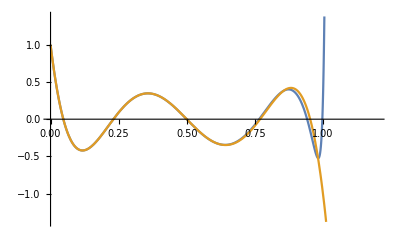
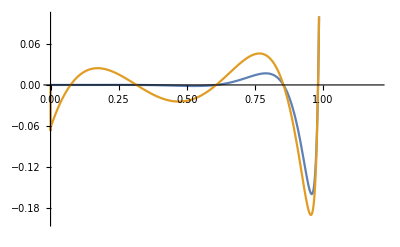

```mathematica
Row[{Pane@Plot[{sln05,sln05hh},{r,0,1.2}],Pane@Plot[{sln05-sln05hh,(sln05-sln05hh)/r^4},{r,0,1.2},PlotRange->{Full,{-0.2,0.1}}]}]
```

```mathematica
sln01=GenEq[199,0,eq,ww[r],r,0,{l->9,Rs->1}];
```

```mathematica
sln01hh=Re@Hypergeometric2F1[-l,1+l,1,r/Rs]/.l->9/.Rs->1;
```

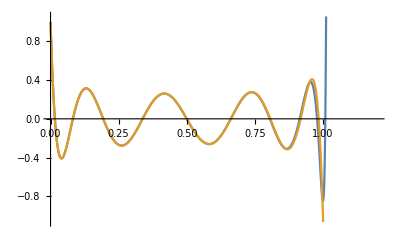
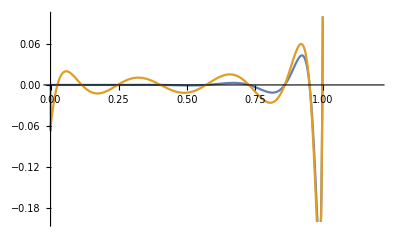

```mathematica
Row[{Pane@Plot[{sln01,sln01hh},{r,0,1.2}],Pane@Plot[{sln01-sln01hh,(sln01-sln01hh)/r^4},{r,0,1.2},PlotRange->{Full,{-0.2,0.1}}]}]
```

```mathematica
Manipulate[Module[{fna=(sln05-sln05hh),fnb= Exp[k/2 r] SphericalBesselY[0,k (1-r)^(1/2)]/(r-1)^(1/4),c},
c=Block[{r=0.8},fna / fnb];
Plot[{r^-3 fna,r^-3 c fnb},{r,0,1},PlotRange->{Full,{-0.2,0.1}}]
],{k, 0.1,40}]
```

#### Особая точка r = Rs (α = ⅈ Rs)

Графики отличаются лишь масштабом левой части!

```mathematica
slni5=GenEq[50,Rs,eq,ww[r],r,ⅈ Rs,{l->5,Rs->1}];
```

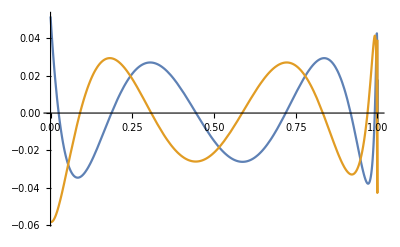
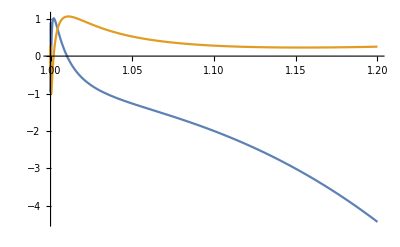

```mathematica
Row[{Pane@Plot[{Re@slni5,Im@slni5},{r,0,1}],Pane@Plot[{Re@slni5, Im@slni5},{r,1,1.2}]}]
```

```mathematica
slnim5=GenEq[50,Rs,eq,ww[r],r,-ⅈ Rs,{l->5,Rs->1}];
```

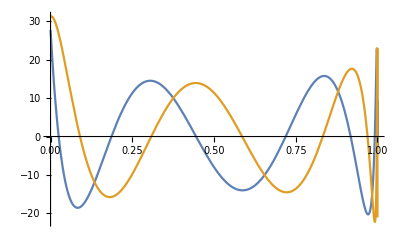
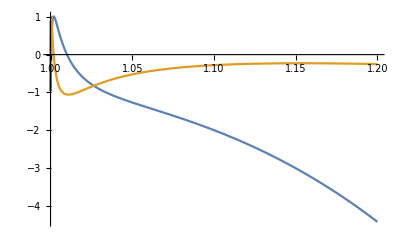

```mathematica
Row[{Pane@Plot[{Re@slnim5,Im@slnim5},{r,0,1}],Pane@Plot[{Re@slnim5, Im@slnim5},{r,1,1.2}]}]
```

```mathematica
slni1=GenEq[50,Rs,eq,ww[r],r,ⅈ Rs,{l->9,Rs->1}];
```

#### Разность фаз в особых точках

```mathematica
Manipulate[Module[{fna=sln05,fnb=Re@(Exp[ⅈ q]slni5),c},
c=Block[{r=0},fna / fnb];
Plot[{fna,c fnb},{r,0,1}]
],{q, 0,2π}]
```

```mathematica
phaseCQ=Sum[(sln05-c Re@(Exp[ⅈ q]slni5))^2,{r,0,1,0.00333}];
Plot3D[phaseCQ,{c,0,13},{q,0,2π}]
```

-Graphics3D-

```mathematica
phaseCQmin=FindMinimum[phaseCQ,{{c,13},{q,0}}]
```

{0.218696,{c→12.9632,q→0.615444}}

Разность фаз отличается для разных L

```mathematica
Manipulate[Module[{fna=sln01,fnb=Re@(Exp[ⅈ q]slni1),c},
c=Block[{r=0},fna / fnb];
Plot[{fna,c fnb},{r,0,1}]
],{q, 0,2π}]
```

Общий случай и закономерность?

```mathematica
PhaseDiff[L_,N1_,N2_]:=Module[{sln0,slni,tbl,min},
sln0=GenEq[N1,0,eq,ww[r],r,0,{l->L,Rs->1}];
slni=GenEq[N2,Rs,eq,ww[r],r,ⅈ Rs,{l->L,Rs->1}];
tbl=Sum[(sln0-c Re@(Exp[ⅈ q]slni))^2,{r,0,1,0.00333}];
min=FindMinimum[tbl,{{c,13},{q,0}}];
min[[2,2,2]]
];
```

```mathematica
phaseCQsmint = Table[{L,PhaseDiff[L,199,50]},{L,0,30}];
```

```mathematica
phaseCQsmint
```

{{0,1.4235},{1,-1.13281},{2,-0.52595},{3,-0.0712937},{4,0.29917},{5,0.615444},{6,0.892561},{7,1.13873},{8,-1.7827},{9,1.55664},{10,-1.40626},{11,-1.24284},{12,-1.09038},{13,-0.945178},{14,-0.80536},{15,-0.670718},{16,-0.541411},{17,-0.417226},{18,-0.297605},{19,-0.181836},{20,-0.0691512},{21,0.0412294},{22,0.14978},{23,0.256131},{24,0.362301},{25,0.459543},{26,0.560774},{27,0.654506},{28,0.75952},{29,0.851169},{30,-0.159498}}

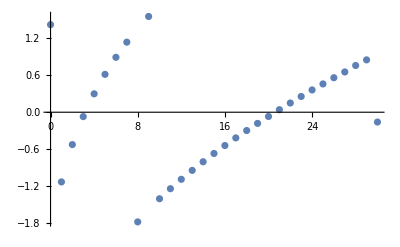

```mathematica
ListPlot[phaseCQsmint]
```

```mathematica
phaseCQsmintf=Module[{vs=phaseCQsmint,i,v,tbl,fx},
tbl={};
i=vs[[1]];
AppendTo[tbl,i];
fx[a_,b_]:=Module[{t=b},While[a-t>π/2,t+=π];t];
fx2[a_,b_]:=Module[{t=b},While[a-t<-π/2,t-=π];t];
Do[AppendTo[tbl,If[Abs[v[[2]]-i[[2]]]>=π/2,{v[[1]],fx[i[[2]],v[[2]]]}, i]]; i = tbl[[-1]],{v,vs[[2;;]]}];
i=tbl[[-2]];
v=tbl[[-1]];
tbl[[-1,2]]=fx2[i[[2]],fx[i[[2]],v[[2]]]];
tbl
]
```

{{0,1.4235},{1,2.00878},{2,2.61564},{3,3.0703},{4,3.44076},{5,3.75704},{6,4.03415},{7,4.28032},{8,4.50048},{9,4.69824},{10,4.87692},{11,5.04035},{12,5.1928},{13,5.33801},{14,5.47783},{15,5.61247},{16,5.74177},{17,5.86596},{18,5.98558},{19,6.10135},{20,6.21403},{21,6.32441},{22,6.43297},{23,6.53932},{24,6.64549},{25,6.74273},{26,6.84396},{27,6.93769},{28,7.04271},{29,7.13435},{30,6.12369}}

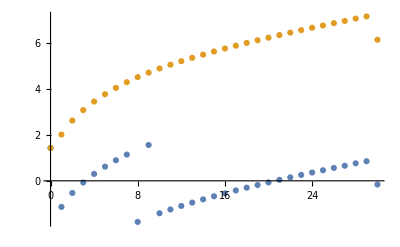

```mathematica
ListPlot[{phaseCQsmint,phaseCQsmintf}]
```

```mathematica
fitPhaseSln=With[{fn=a + c x^(1/2)},fn/.FindFit[phaseCQsmintf[[;;-2]],fn,{a,b,c,d, e},x]]
```

1.26054+1.10786 √x

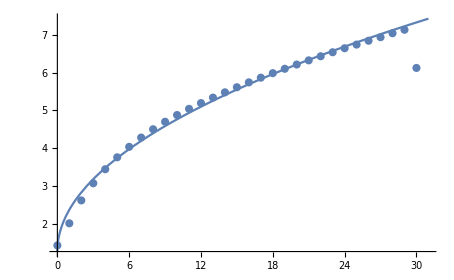

```mathematica
Show[Plot[Re@fitPhaseSln,{x,0,31}],ListPlot[phaseCQsmintf],PlotRange->All]
```

#### Численное решение

```mathematica
NumSln[eq_,fn_,r_,gsln_,ass_,rmax_]:=Module[{t1=0.333,t2=(*1.006*)1.5,eql,v1,v2,d1,d2,f1,f2,fh=Head@fn,eps=10^-8,z},
v1=gsln/.r->t1;
v2=gsln/.r->t2;
d1=Evaluate[D[gsln,r]]/.r->t1;
d2=Evaluate[D[gsln,r]]/.r->t2;
eql=eq//.ass;
f1=Quiet@NDSolve[{eql==0,fh[t1]==v1,fh'[t1]==d1},fh,{r,0+eps,1-eps}, MaxSteps->Infinity,AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->100][[1,1,2]];
f2=Quiet@NDSolve[{eql==0,fh[t2]==v2,fh'[t2]==d2},fh,{r,1+eps,rmax}, MaxSteps->Infinity,AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->100][[1,1,2]];
Function[{z},Piecewise[{{f1[z],eps<z&&z<1-eps},{f2[z],1+eps<z&&z<rmax}},0]]
];
```

```mathematica
slnn5=NumSln[eq,ww[r],r,slni5,{l->5,Rs->1},1000];
```

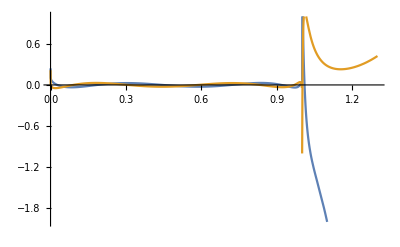

```mathematica
Plot[{Re@slnn5[r],Im@slnn5[r]},{r,0,1.3},PlotRange->{Full,{-2,1}}]
```

```mathematica
slnnm5=NumSln[eq,ww[r],r,slnim5,{l->5,Rs->1},1000];
```

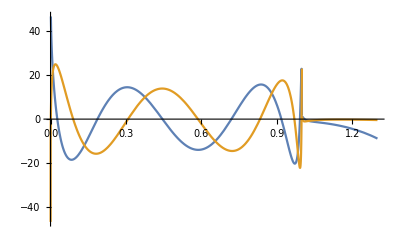

```mathematica
Plot[{Re@slnnm5[r],Im@slnnm5[r]},{r,0,1.3}]
```

```mathematica
slnns5=Function[{r},slnn5[r]-slnnm5[r]];
```

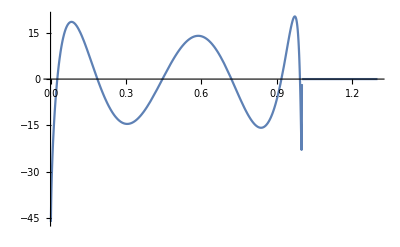

```mathematica
Plot[{Re@slnns5[r],Im@slnnms5[r]},{r,0,1.3}]
```

#### Графики функций

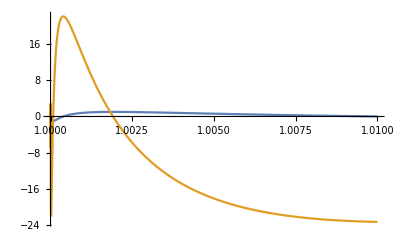

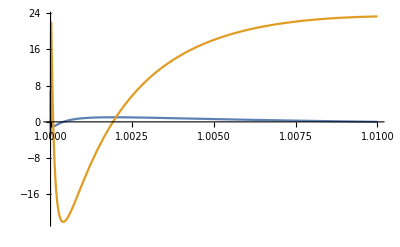

```mathematica
Plot[{Re@slni5,-22Im@slni5},{r,1,1.01}]
Plot[{Re@slnim5,-22Im@slnim5},{r,1,1.01}]
```

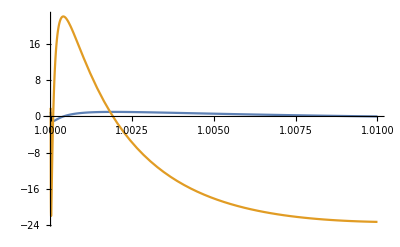

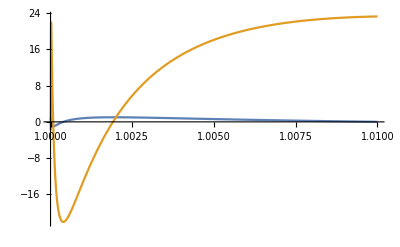

```mathematica
Plot[{Re@slnn5[r],-22Im@slnn5[r]},{r,1,1.01}]
Plot[{Re@slnnm5[r],-22Im@slnnm5[r]},{r,1,1.01}]
```

```mathematica
Animate[Plot[{Re@(Exp[-ⅈ t]slnnm5[r]),-Im@(Exp[-ⅈ t]slnnm5[r])},{r,0,1},PlotRange->{Full,{-50,50}}],{t,0,20 2π},AnimationRate->0.03]
Animate[Plot[{Re@(Exp[-ⅈ t]slnnm5[r]),-Im@(Exp[-ⅈ t]slnnm5[r])},{r,1,20},PlotRange->{Full,{-20000,20000}}],{t,0,20 2π},AnimationRate->0.03]
```

```mathematica
slnnms5=Function[{r},slnn5[r]-slnnm5[r]];
```

```mathematica
Animate[Plot[{Re@(Exp[-ⅈ t]slnnm5[r]),-Im@(Exp[-ⅈ t]slnns5[r])},{r,0,1},PlotRange->{Full,{-50,50}}],{t,0,20 2π},AnimationRate->0.03]
Animate[Plot[{Re@(Exp[-ⅈ t]slnns5[r]),-Im@(Exp[-ⅈ t]slnns5[r])},{r,1,20},PlotRange->{Full,{-1500,1500}}],{t,0,20 2π},AnimationRate->0.03]
```

```mathematica
Animate[Plot[{Re@(Exp[-ⅈ t] (SphericalHankelH1[5,r]+SphericalHankelH2[5,r])),Im@(Exp[-ⅈ t] (SphericalHankelH1[5,r]+SphericalHankelH2[5,r]))},{r,1,20},PlotRange->{Full,{-0.6,0.6}}],{t,0,20 2π},AnimationRate->0.03]
```

```mathematica
Animate[Plot[Re@(Exp[ⅈ t](slnn5[r]+ⅇ^(ⅈ π/4) slnnm5[r])/10000),{r,0,1}],{t,0,10}]
```

#### Энергия-импульс ШВ

```mathematica
Ricci[{ct,r,u,w},GGSW];
```

```mathematica
Tij =Table[SSum[1/2ð[fs,k]ð[fs,l](tmu[i,k]tmu[j,l]-tmu[i,j]tmu[k,l]),k,l],{i,0,3},{j,0,3}];
```

```mathematica
Tijs=Table[(gd Tij[[ii,jj]]//CovExpand)//.SSum2SumRules[{#,0,3}&]/.TensorChristoffel[]->cs2/.tmu->hh//S,{ii,1,4},{jj,1,4}];
```

```mathematica
Tijsr=(Tijs//ExpandAll)/.{(x:fs|ð[fs,_])(y:fs|ð[fs,_]):>1/2Re[x Conjugate[y]], (x:fs|ð[fs,_])^2:>1/2Re[x Conjugate[x]]};
```

```mathematica
Tijr=EvaluateAt[Tijsr,fs:>f[ct,r,u]]//S;
```

```mathematica
Tijrn5=Tijr/.f->Function[{ct,r,u},LegendreP[5,Cos[u]] ⅇ^(-ⅈ ct)slnn5[r]];
Tijrnm5=Tijr/.f->Function[{ct,r,u},LegendreP[5,Cos[u]] ⅇ^(-ⅈ ct)slnnm5[r]];
Tijrns5=Tijr/.f->Function[{ct,r,u},LegendreP[5,Cos[u]] ⅇ^(-ⅈ ct)slnns5[r]];
```

```mathematica
{een5,UUn5}=evalTijS[dTij@Tijrn5,5,u]/.Rs->1;
{eenm5,UUnm5}=evalTijS[dTij@Tijrnm5,5,u]/.Rs->1;
{eens5,UUns5}=evalTijS[dTij@Tijrns5,5,u]/.Rs->1;
```

#### Энергия-импульс графики

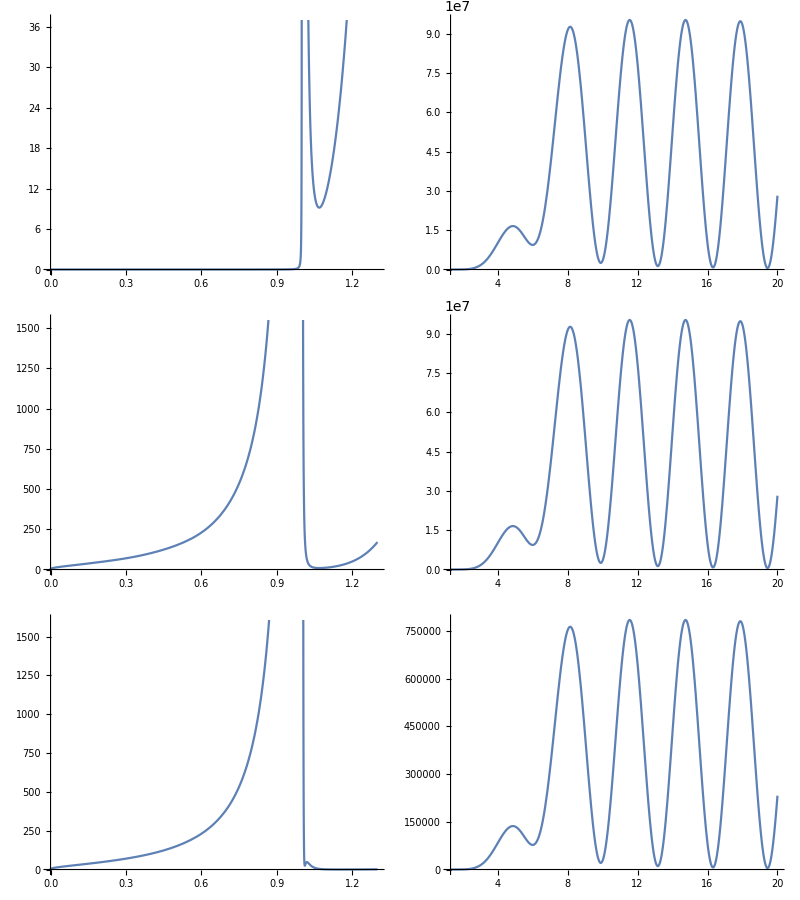

```mathematica
Grid@Table[{Pane@Plot[Re@ee/.u->1.33//Evaluate,{r,0,1.3}], Pane@Plot[Re@ee/.u->1.33//Evaluate,{r,1.3,20},PlotRange->Full]},{ee,{een5, eenm5, eens5}}]
```

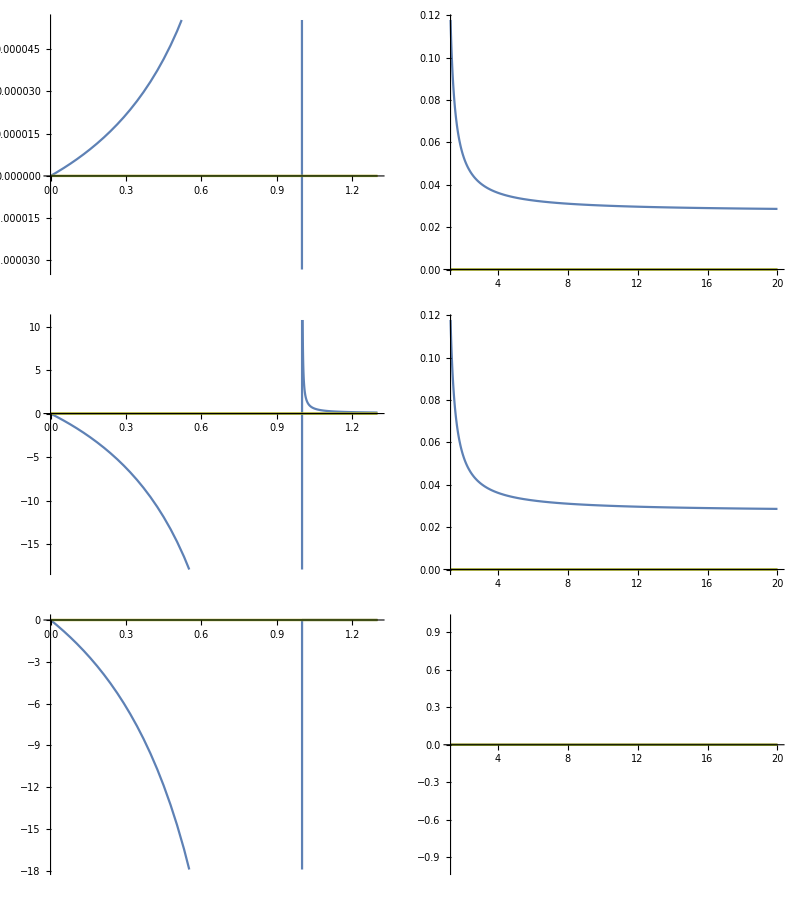

```mathematica
Grid@Table[{Pane@Plot[Re@ee/.u->1.33//Evaluate,{r,0,1.3}], Pane@Plot[Abs@ee/.u->1.33//Evaluate,{r,1.3,20},PlotRange->Full]},{ee,{UUn5, UUnm5, UUns5}}]
```

```mathematica
ParametricPlot3D[{3r Cos[u],3r Sin[u],10^-7 Re@een5//Evaluate},{r,0,17},{u,0,π},PlotRange->{Full,Full,{0,50}},PlotPoints->20]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{3r Cos[u],3r Sin[u],10^-5 Re@eens5//Evaluate},{r,0,17},{u,0,π},PlotRange->{Full,Full,{0,50}},PlotPoints->20]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{3r Cos[u],3r Sin[u],-5 10^2 Re@UUn5[[1]]//Evaluate},{r,0,17},{u,0,π},PlotRange->{Full,Full,{0,50}},PlotPoints->20]
```

-Graphics3D-

#### Сохранение

```mathematica
seq=eq;
ssln05=sln05;
sslni5=slni5;
sslnim5=slnim5;
sslnn5=slnn5;
sslnnm5=slnnm5;
{seen5,sUUn5}={een5,UUn5};
{seenm5,sUUnm5}={eenm5,UUnm5};
{seens5,sUUns5}={eens5,UUns5};
```

### Скалярное поле в метрике Пенлеве

Данный подраздел содержит некорректные вычисления и неверные результаты. См. раздел Результаты.

```mathematica
eq=(2 l+2 l^2+r (-2 r+3 ⅈ √(Rs/r))) ww[r]+2 ((-2 r+Rs+2 ⅈ r^2 √(Rs/r)) ww'[r]+r (-r+Rs) ww''[r]);
```

Особые точки

```mathematica
Pqa[eq, ww[r],r,0]
Pqa[eq, ww[r],r,Rs]
```

{{1,0},{{α→0},{α→0}}}

{{1-2 ⅈ Rs,0},{{α→0},{α→2 ⅈ Rs}}}

#### Особая точка r = 0

```mathematica
sln05=GenEq[399,0,eq,ww[r],r,0,{l->5,Rs->1}];
```

```mathematica
sln05hh=Re@Hypergeometric2F1[-l,1+l,1,r/Rs]/.l->5/.Rs->1;
```

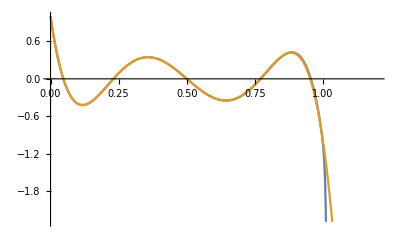
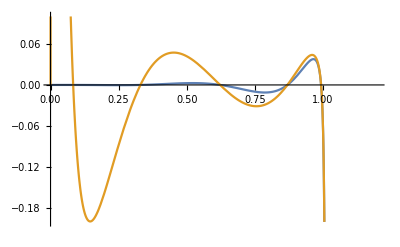

```mathematica
Row[{Pane@Plot[{sln05,sln05hh},{r,0,1.2}],Pane@Plot[{sln05-sln05hh,(sln05-sln05hh)/r^4},{r,0,1.2},PlotRange->{Full,{-0.2,0.1}}]}]
```

```mathematica
sln01=GenEq[199,0,eq,ww[r],r,0,{l->9,Rs->1}];
```

```mathematica
sln01hh=Re@Hypergeometric2F1[-l,1+l,1,r/Rs]/.l->9/.Rs->1;
```

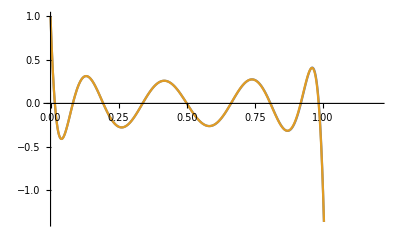
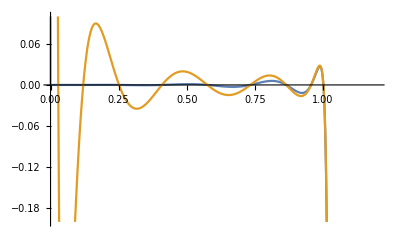

```mathematica
Row[{Pane@Plot[{sln01,sln01hh},{r,0,1.2}],Pane@Plot[{sln01-sln01hh,(sln01-sln01hh)/r^4},{r,0,1.2},PlotRange->{Full,{-0.2,0.1}}]}]
```

#### Особая точка r = Rs (α = 0, 2 ⅈ Rs)

```mathematica
slni5=GenEq[399,Rs,eq,ww[r],r,2ⅈ Rs,{l->5,Rs->1}];
```

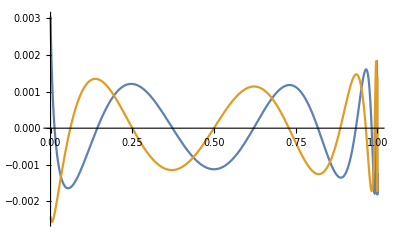
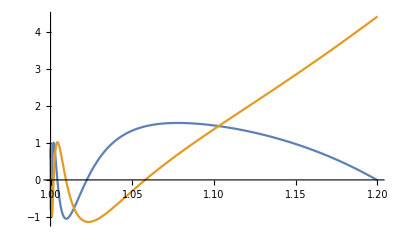

```mathematica
Row[{Pane@Plot[{Re@slni5,Im@slni5},{r,0,1}],Pane@Plot[{Re@slni5,Im@slni5},{r,1,1.2}]}]
```

```mathematica
slnim5=GenEq[399,Rs,eq,ww[r],r,0,{l->5,Rs->1}];
```

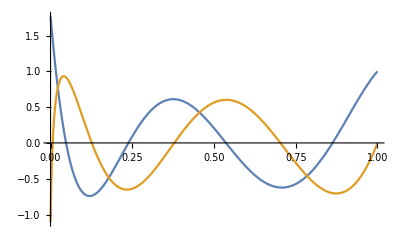
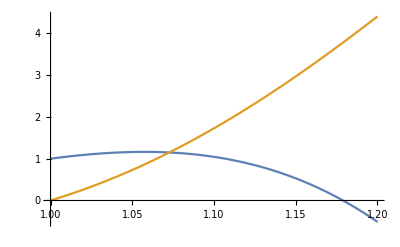

```mathematica
Row[{Pane@Plot[{Re@slnim5,Im@slnim5},{r,0,1}],Pane@Plot[{Re@slnim5,Im@slnim5},{r,1,1.2}]}]
```

#### Разность фаз в особых точках

Решения совсем разные!

```mathematica
Manipulate[Module[{fna=sln05,fnb=Re@(Exp[ⅈ q]slni5),c},
c=Block[{r=0},fna / fnb];
Plot[{fna,c fnb},{r,0,1}]
],{q, 0,2π}]
```

```mathematica
Manipulate[Module[{fna=sln05,fnb=Re@(Exp[ⅈ q]slnim5),c},
c=Block[{r=0},fna / fnb];
Plot[{fna,c fnb},{r,0,1}]
],{q, 0,2π}]
```

#### Численное решение

```mathematica
NumSlnP[eq_,fn_,r_,gsln_,ass_,rmax_]:=Module[{t1=0.333,t2=1.006,eql,v1,v2,d1,d2,f1,f2,fh=Head@fn,eps=10^-8,z},
v1=gsln/.r->t1;
v2=gsln/.r->t2;
d1=Evaluate[D[gsln,r]]/.r->t1;
d2=Evaluate[D[gsln,r]]/.r->t2;
eql=eq//.ass;
f1=Quiet@NDSolve[{eql==0,fh[t1]==v1,fh'[t1]==d1},fh,{r,0+eps,1-eps}, MaxSteps->Infinity,AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->100][[1,1,2]];
f2=Quiet@NDSolve[{eql==0,fh[t2]==v2,fh'[t2]==d2},fh,{r,1+eps,rmax}, MaxSteps->Infinity,AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->100][[1,1,2]];
Function[{z},Piecewise[{{f1[z],eps<z&&z<1-eps},{f2[z],1+eps<z&&z<rmax}},0]]
];
```

```mathematica
slnn5=NumSlnP[eq,ww[r],r,slni5,{l->5,Rs->1},1000];
```

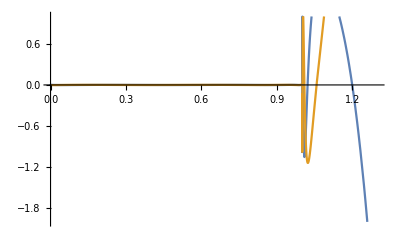

```mathematica
Plot[{Re@slnn5[r],Im@slnn5[r]},{r,0,1.3},PlotRange->{Full,{-2,1}}]
```

```mathematica
slnnm5=NumSlnP[eq,ww[r],r,slnim5,{l->5,Rs->1},1000];
```

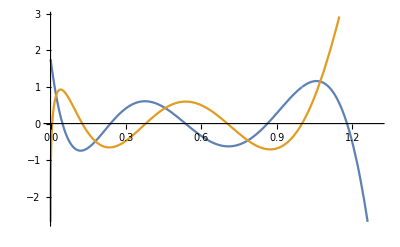

```mathematica
Plot[{Re@slnnm5[r],Im@slnnm5[r]},{r,0,1.3}]
```

```mathematica
slnns5=Function[{r},slnn5[r]-slnnm5[r]];
```

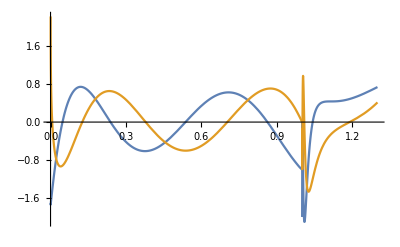

```mathematica
Plot[{Re@slnns5[r],Im@slnns5[r]},{r,0,1.3}]
```

#### Графики функций

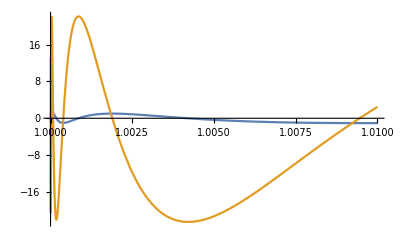

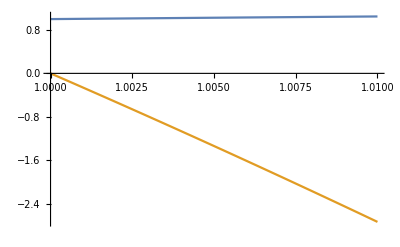

```mathematica
Plot[{Re@slni5,-22Im@slni5},{r,1,1.01}]
Plot[{Re@slnim5,-22Im@slnim5},{r,1,1.01}]
```

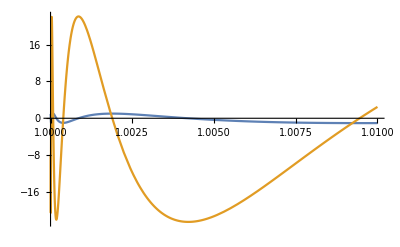

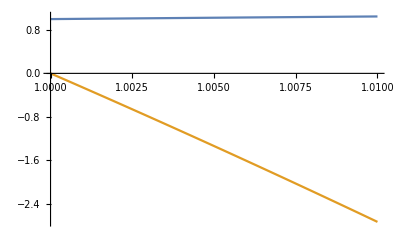

```mathematica
Plot[{Re@slnn5[r],-22Im@slnn5[r]},{r,1,1.01}]
Plot[{Re@slnnm5[r],-22Im@slnnm5[r]},{r,1,1.01}]
```

```mathematica
Animate[Plot[{Re@(Exp[-ⅈ t]slnnm5[r]),-Im@(Exp[-ⅈ t]slnnm5[r])},{r,0,1},PlotRange->{Full,{-5,5}}],{t,0,20 2π},AnimationRate->0.03]
Animate[Plot[{Re@(Exp[-ⅈ t]slnnm5[r]),-Im@(Exp[-ⅈ t]slnnm5[r])},{r,1,20},PlotRange->{Full,{-20000,20000}}],{t,0,20 2π},AnimationRate->0.03]
```

```mathematica
Animate[Plot[{Re@(Exp[-ⅈ t]slnnm5[r]),-Im@(Exp[-ⅈ t]slnns5[r])},{r,0,1},PlotRange->{Full,{-5,5}}],{t,0,20 2π},AnimationRate->0.03]
Animate[Plot[{Re@(Exp[-ⅈ t]slnns5[r]),-Im@(Exp[-ⅈ t]slnns5[r])},{r,1,20},PlotRange->{Full,{-1500,1500}}],{t,0,20 2π},AnimationRate->0.03]
```

```mathematica
Animate[Plot[{Re@(Exp[-ⅈ t] (SphericalHankelH1[5,r]+SphericalHankelH2[5,r])),Im@(Exp[-ⅈ t] (SphericalHankelH1[5,r]+SphericalHankelH2[5,r]))},{r,1,20},PlotRange->{Full,{-0.6,0.6}}],{t,0,20 2π},AnimationRate->0.03]
```

#### Энергия-импульс ПВ

```mathematica
Ricci[{ct,r,u,w},GGPW];
```

```mathematica
Tij =Table[SSum[1/2ð[fs,k]ð[fs,l](tmu[i,k]tmu[j,l]-tmu[i,j]tmu[k,l]),k,l],{i,0,3},{j,0,3}];
```

```mathematica
Tijs=Table[(gd Tij[[ii,jj]]//CovExpand)//.SSum2SumRules[{#,0,3}&]/.TensorChristoffel[]->cs2/.tmu->hh//S,{ii,1,4},{jj,1,4}];
```

```mathematica
Tijsr=(Tijs//ExpandAll)/.{(x:fs|ð[fs,_])(y:fs|ð[fs,_]):>1/2Re[x Conjugate[y]], (x:fs|ð[fs,_])^2:>1/2Re[x Conjugate[x]]};
```

```mathematica
Tijr=EvaluateAt[Tijsr,fs:>f[ct,r,u]]//S;
```

```mathematica
Tijrn5=Tijr/.f->Function[{ct,r,u},LegendreP[5,Cos[u]] ⅇ^(ⅈ ct)slnn5[r]];
Tijrnm5=Tijr/.f->Function[{ct,r,u},LegendreP[5,Cos[u]] ⅇ^(ⅈ ct)slnnm5[r]];
Tijrns5=Tijr/.f->Function[{ct,r,u},LegendreP[5,Cos[u]] ⅇ^(ⅈ ct)slnns5[r]];
```

```mathematica
{een5,UUn5}=evalTijS[dTij@Tijrn5,5,u]/.Rs->1;
{eenm5,UUnm5}=evalTijS[dTij@Tijrnm5,5,u]/.Rs->1;
{eens5,UUns5}=evalTijS[dTij@Tijrns5,5,u]/.Rs->1;
```

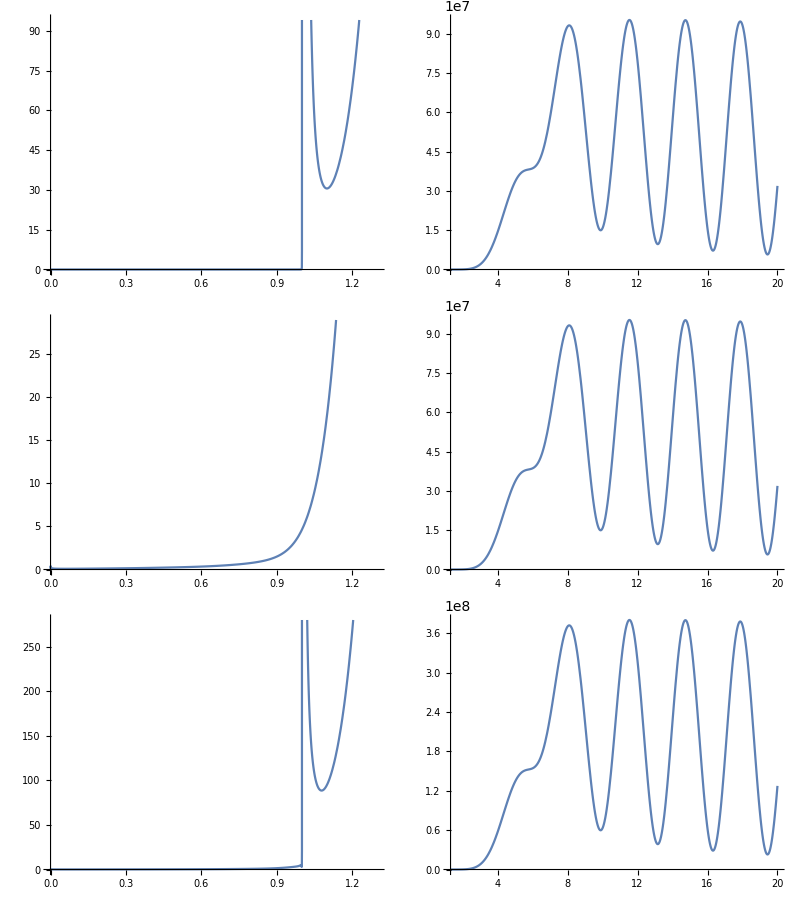

```mathematica
Grid@Table[{Pane@Plot[Re@ee/.u->1.33//Evaluate,{r,0,1.3}], Pane@Plot[Re@ee/.u->1.33//Evaluate,{r,1.3,20},PlotRange->Full]},{ee,{een5, eenm5, eens5}}]
```

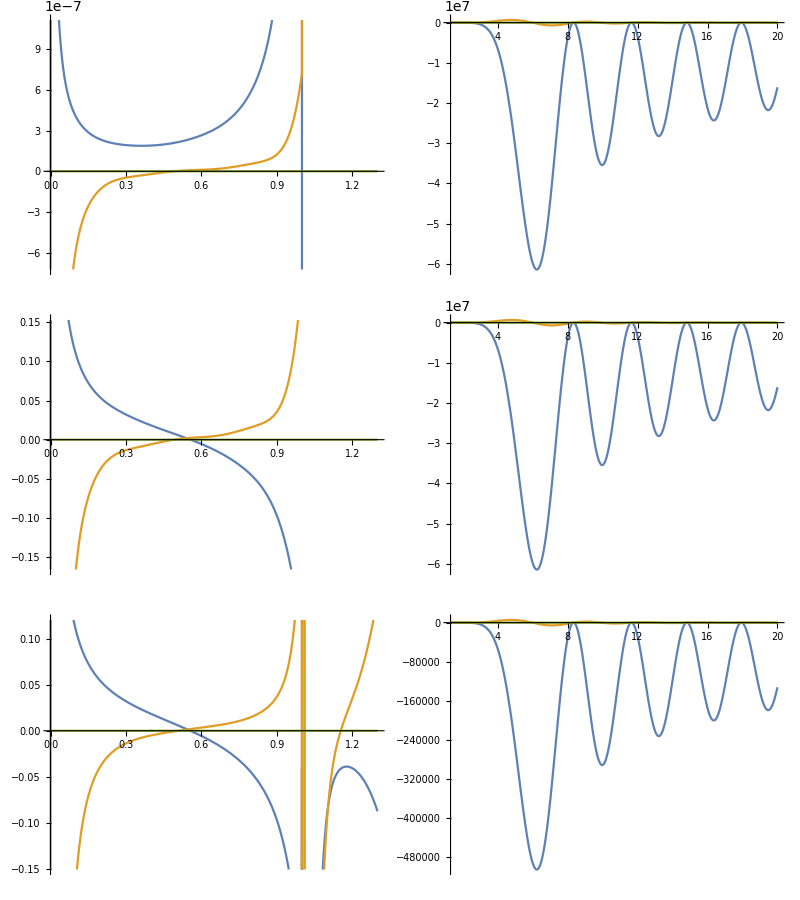

```mathematica
Grid@Table[{Pane@Plot[Re@ee/.u->1.33//Evaluate,{r,0,1.3}], Pane@Plot[Re@ee/.u->1.33//Evaluate,{r,1.3,20},PlotRange->Full]},{ee,{UUn5, UUnm5, UUns5}}]
```

```mathematica
ParametricPlot3D[{3r Cos[u],3r Sin[u],10^-7 Re@een5//Evaluate},{r,0,17},{u,0,π},PlotRange->{Full,Full,{0,50}},PlotPoints->20]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{3r Cos[u],3r Sin[u],10^-5 Re@eens5//Evaluate},{r,0,17},{u,0,π},PlotRange->{Full,Full,{0,50}},PlotPoints->20]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{3r Cos[u],3r Sin[u],-5 10^2 Re@UUn5[[1]]//Evaluate},{r,0,17},{u,0,π},PlotRange->{Full,Full,{0,50}},PlotPoints->20]
```

-Graphics3D-

#### Результаты

Теория идет прахом, поскольку на самом деле Sqrt[x] не разлагается в ряд в окрестности нуля.

```mathematica
Series[√x,{x,x0,3}]//Normal
```

(x-x0)^3/(16 x0^(5/2))-(x-x0)^2/(8 x0^(3/2))+(x-x0)/(2 √x0)+√x0

```mathematica
Limit[%,x0->0]
```

x^3 ∞

### Векторное поле в метрике Минковского

```mathematica
Ricci[{ct,r,u,w},GGM];
```

```mathematica
eq=-2 (l+l^2-r^2) ww[r]+2 r^2 ww''[r];
```

#### Решения

```mathematica
DSolve[eq==0,ww[r],r]//FullSimplify
```

{{ww[r]→√r (BesselJ[1/2+l,r] C[1]+BesselY[1/2+l,r] C[2])}}

```mathematica
slnn5=Function[{r},r SphericalHankelH1[5,r]];
slnnm5=Function[{r},r SphericalHankelH2[5,r]];
```

```mathematica
slnns5=Function[{r},slnn5[r]+slnnm5[r]];
```

#### Энергия-импульс

```mathematica
intro[tF]:=tF[i_,k_]:>ð[ta[i],Cov[k]]-ð[ta[k],Cov[i]];
```

```mathematica
Tij = Table[SSum[-tmu[s,k]tmu[i,j]tmu[m,l]tF[j,m]tF[s,l]+1/4tmu[i,k]tmu[j,l]tmu[s,m]tF[l,m]tF[j,s],s,j,m,l],{i,0,3},{k,0,3}]//rewriteT[tF];
```

```mathematica
Tijs=Table[(gd Tij[[ii,jj]]//CovExpand)//.SSum2SumRules[{#,0,3}&]/.TensorChristoffel[]->cs2/.tmu->hh//S,{ii,1,4},{jj,1,4}];
```

```mathematica
Tijsr=(Tijs//ExpandAll)/.{(x:ta[__]|ð[ta[__],_])(y:ta[__]|ð[ta[__],_]):>1/2Re[x Conjugate[y]], (x:ta[__]|ð[ta[__],_])^2:>1/2Re[x Conjugate[x]]};
```

```mathematica
Tijr=EvaluateAt[Tijsr,ta[i_]:>{0,0,0,Sin[u]f3[ct,r,u]}[[i+1]]];
```

```mathematica
Tijrn5=Tijr/.f3->Function[{ct,r,u},D[LegendreP[5,Cos[u]],u] ⅇ^(-ⅈ ct)slnn5[r]];
Tijrnm5=Tijr/.f3->Function[{ct,r,u},D[LegendreP[5,Cos[u]],u] ⅇ^(-ⅈ ct)slnnm5[r]];
Tijrns5=Tijr/.f3->Function[{ct,r,u},D[LegendreP[5,Cos[u]],u] ⅇ^(-ⅈ ct)slnns5[r]];
```

```mathematica
{een5,UUn5}=evalTijS[dTij@Tijrn5,5,u]/.Rs->1;
{eenm5,UUnm5}=evalTijS[dTij@Tijrnm5,5,u]/.Rs->1;
{eens5,UUns5}=evalTijS[dTij@Tijrns5,5,u]/.Rs->1;
```

#### Сохранение

```mathematica
vmeq=eq;
vmslnn5=slnn5;
vmslnnm5=slnnm5;
vmslnns5=slnns5;
{vmeen5,vmUUn5}={een5,UUn5};
{vmeenm5,vmUUnm5}={eenm5,UUnm5};
{vmeens5,vmUUns5}={eens5,UUns5};
```

### Векторное поле в метрике Шварцшильда

```mathematica
eq=((r^3+l (-r+Rs)+l^2 (-r+Rs)) ww[r]+(r-Rs) (Rs ww'[r]+r (r-Rs) ww''[r]));
```

Особые точки

```mathematica
Pqa[eq, ww[r],r,0]
Pqa[eq, ww[r],r,Rs]
```

{{-1,0},{{α→0},{α→2}}}

{{1,Rs^2},{{α→-ⅈ Rs},{α→ⅈ Rs}}}

#### Особая точка r = 0

```mathematica
sln05=GenEq[199,0,eq,ww[r],r,2,{l->5,Rs->1}];
```

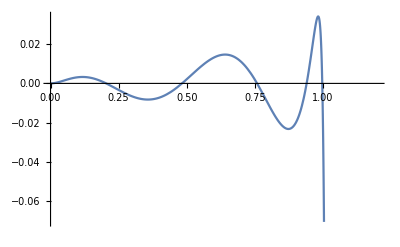

```mathematica
Plot[{sln05},{r,0,1.2}]
```

#### Особая точка r = Rs (α = ⅈ Rs)

Графики отличаются лишь масштабом левой части!

```mathematica
slni5=GenEq[199,Rs,eq,ww[r],r,ⅈ Rs,{l->5,Rs->1}];
```

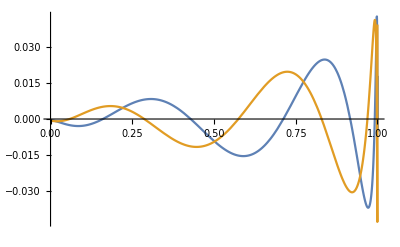
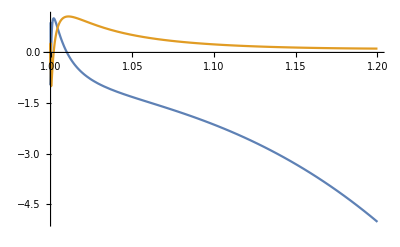

```mathematica
Row[{Pane@Plot[{Re@slni5,Im@slni5},{r,0,1}],Pane@Plot[{Re@slni5, Im@slni5},{r,1,1.2}]}]
```

```mathematica
slnim5=GenEq[199,Rs,eq,ww[r],r,-ⅈ Rs,{l->5,Rs->1}];
```

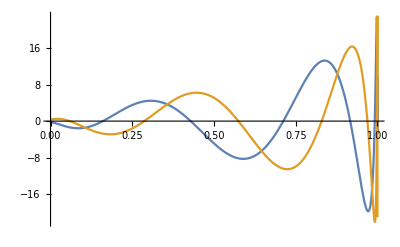
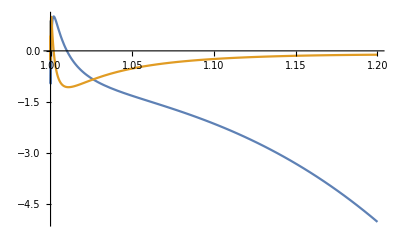

```mathematica
Row[{Pane@Plot[{Re@slnim5,Im@slnim5},{r,0,1}],Pane@Plot[{Re@slnim5, Im@slnim5},{r,1,1.2}]}]
```

#### Численное решение

```mathematica
NumSln[eq_,fn_,r_,gsln_,ass_,rmax_]:=Module[{t1=0.333,t2=(*1.006*)1.5,eql,v1,v2,d1,d2,f1,f2,fh=Head@fn,eps=10^-8,z},
v1=gsln/.r->t1;
v2=gsln/.r->t2;
d1=Evaluate[D[gsln,r]]/.r->t1;
d2=Evaluate[D[gsln,r]]/.r->t2;
eql=eq//.ass;
f1=Quiet@NDSolve[{eql==0,fh[t1]==v1,fh'[t1]==d1},fh,{r,0+eps,1-eps}, MaxSteps->Infinity,AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->100][[1,1,2]];
f2=Quiet@NDSolve[{eql==0,fh[t2]==v2,fh'[t2]==d2},fh,{r,1+eps,rmax}, MaxSteps->Infinity,AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->100][[1,1,2]];
Function[{z},Piecewise[{{f1[z],eps<z&&z<1-eps},{f2[z],1+eps<z&&z<rmax}},0]]
];
```

```mathematica
slnn5=NumSln[eq,ww[r],r,slni5,{l->5,Rs->1},1000];
```

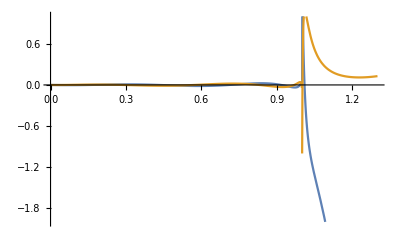

```mathematica
Plot[{Re@slnn5[r],Im@slnn5[r]},{r,0,1.3},PlotRange->{Full,{-2,1}}]
```

```mathematica
slnnm5=NumSln[eq,ww[r],r,slnim5,{l->5,Rs->1},1000];
```

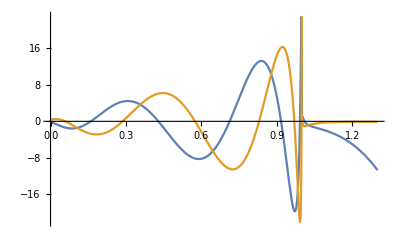

```mathematica
Plot[{Re@slnnm5[r],Im@slnnm5[r]},{r,0,1.3}]
```

```mathematica
slnns5=Function[{r},slnn5[r]-slnnm5[r]];
```

#### Графики функций

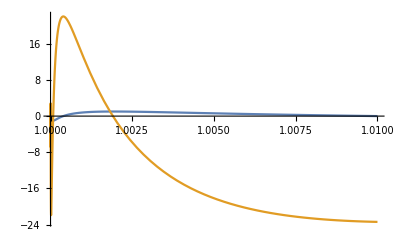

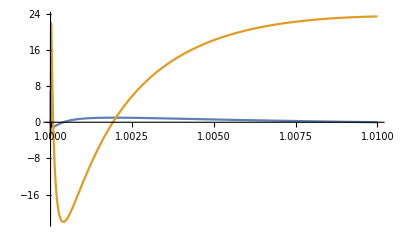

```mathematica
Plot[{Re@slni5,-22Im@slni5},{r,1,1.01}]
Plot[{Re@slnim5,-22Im@slnim5},{r,1,1.01}]
```

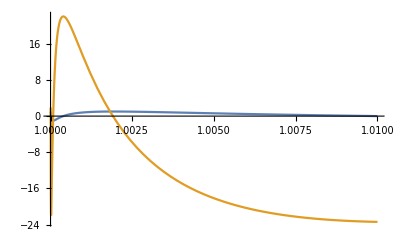

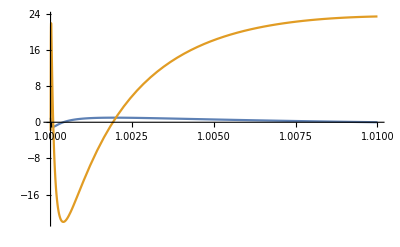

```mathematica
Plot[{Re@slnn5[r],-22Im@slnn5[r]},{r,1,1.01}]
Plot[{Re@slnnm5[r],-22Im@slnnm5[r]},{r,1,1.01}]
```

```mathematica
Animate[Plot[{Re@(Exp[-ⅈ t]slnnm5[r]),-Im@(Exp[-ⅈ t]slnnm5[r])},{r,0,1},PlotRange->{Full,{-50,50}}],{t,0,20 2π},AnimationRate->0.03]
Animate[Plot[{Re@(Exp[-ⅈ t]slnnm5[r]),-Im@(Exp[-ⅈ t]slnnm5[r])},{r,1,20},PlotRange->{Full,{-60000,60000}}],{t,0,20 2π},AnimationRate->0.03]
```

#### Энергия-импульс ШВ

```mathematica
Ricci[{ct,r,u,w},GGSW];
```

```mathematica
intro[tF]:=tF[i_,k_]:>ð[ta[i],Cov[k]]-ð[ta[k],Cov[i]];
```

```mathematica
Tij = Table[SSum[-tmu[s,k]tmu[i,j]tmu[m,l]tF[j,m]tF[s,l]+1/4tmu[i,k]tmu[j,l]tmu[s,m]tF[l,m]tF[j,s],s,j,m,l],{i,0,3},{k,0,3}]//rewriteT[tF];
```

```mathematica
Tijs=Table[(gd Tij[[ii,jj]]//CovExpand)//.SSum2SumRules[{#,0,3}&]/.TensorChristoffel[]->cs2/.tmu->hh//S,{ii,1,4},{jj,1,4}];
```

```mathematica
Tijsr=(Tijs//ExpandAll)/.{(x:ta[__]|ð[ta[__],_])(y:ta[__]|ð[ta[__],_]):>1/2Re[x Conjugate[y]], (x:ta[__]|ð[ta[__],_])^2:>1/2Re[x Conjugate[x]]};
```

```mathematica
Tijr=EvaluateAt[Tijsr,ta[i_]:>{0,0,0,Sin[u]f3[ct,r,u]}[[i+1]]];
```

```mathematica
Tijrn5=Tijr/.f3->Function[{ct,r,u},D[LegendreP[5,Cos[u]],u] ⅇ^(-ⅈ ct)slnn5[r]];
Tijrnm5=Tijr/.f3->Function[{ct,r,u},D[LegendreP[5,Cos[u]],u] ⅇ^(-ⅈ ct)slnnm5[r]];
Tijrns5=Tijr/.f3->Function[{ct,r,u},D[LegendreP[5,Cos[u]],u] ⅇ^(-ⅈ ct)slnns5[r]];
```

```mathematica
{een5,UUn5}=evalTijS[dTij@Tijrn5,5,u]/.Rs->1;
{eenm5,UUnm5}=evalTijS[dTij@Tijrnm5,5,u]/.Rs->1;
{eens5,UUns5}=evalTijS[dTij@Tijrns5,5,u]/.Rs->1;
```

#### Энергия-импульс графики

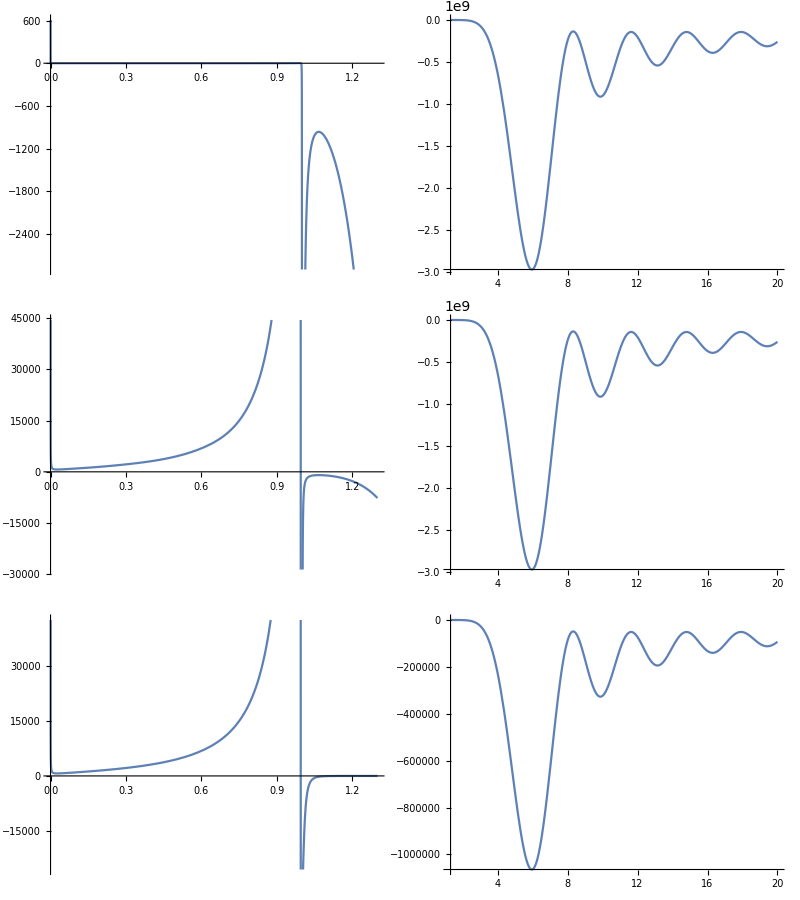

```mathematica
Grid@Table[{Pane@Plot[Re@ee/.u->1.33//Evaluate,{r,0,1.3}], Pane@Plot[Re@ee/.u->1.33//Evaluate,{r,1.3,20},PlotRange->Full]},{ee,{een5, eenm5, eens5}}]
```

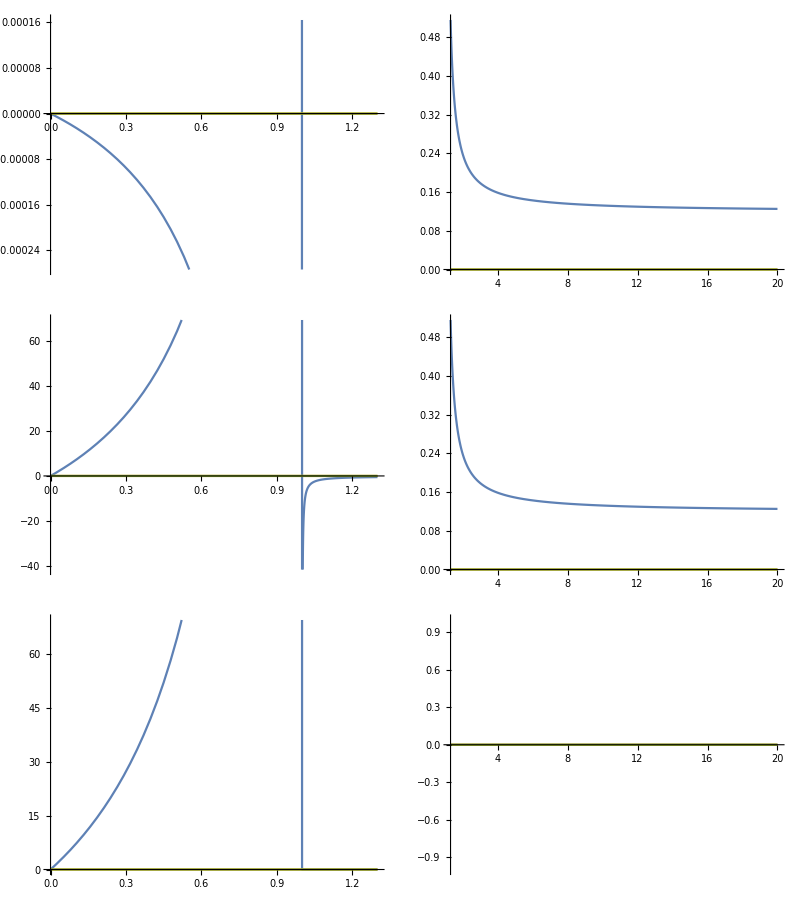

```mathematica
Grid@Table[{Pane@Plot[Re@ee/.u->1.33//Evaluate,{r,0,1.3}], Pane@Plot[Abs@ee/.u->1.33//Evaluate,{r,1.3,20},PlotRange->Full]},{ee,{UUn5, UUnm5, UUns5}}]
```

```mathematica
ParametricPlot3D[{3r Cos[u],3r Sin[u],10^-7 Re@een5//Evaluate},{r,0,17},{u,0,π},PlotRange->{Full,Full,{0,50}},PlotPoints->20]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{3r Cos[u],3r Sin[u],10^-5 Re@eens5//Evaluate},{r,0,17},{u,0,π},PlotRange->{Full,Full,{0,50}},PlotPoints->20]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{3r Cos[u],3r Sin[u],-5 10^2 Re@UUn5[[1]]//Evaluate},{r,0,17},{u,0,π},PlotRange->{Full,Full,{0,50}},PlotPoints->20]
```

-Graphics3D-

#### Сохранение

```mathematica
veq=eq;
vsln05=sln05;
vslni5=slni5;
vslnim5=slnim5;
vslnn5=slnn5;
vslnnm5=slnnm5;
{veen5,vUUn5}={een5,UUn5};
{veenm5,vUUnm5}={eenm5,UUnm5};
{veens5,vUUns5}={eens5,UUns5};
```

### Сравнение с решениями в метрике Минковского и графики для отчета

#### Вспомогательное

```mathematica
SavePlot[fname_][expr_]:=Module[{out=FileNameJoin[{NotebookDirectory[], "dist", fname<>".png"}]},Export[out, Rasterize[expr,ImageResolution->300]]; expr];
```

#### Сравнение уравнений

```mathematica
seq
veq
```

(r^3+l (-r+Rs)+l^2 (-r+Rs)) ww[r]+(r-Rs) ((2 r-Rs) ww'[r]+r (r-Rs) ww''[r])

(r^3+l (-r+Rs)+l^2 (-r+Rs)) ww[r]+(r-Rs) (Rs ww'[r]+r (r-Rs) ww''[r])

```mathematica
Coefficient[seq,{ww[r],ww'[r],ww''[r]}]/Coefficient[seq,ww''[r]]//Apart
Coefficient[veq,{ww[r],ww'[r],ww''[r]}]/Coefficient[seq,ww''[r]]//Apart
```

{r^2/(-r+Rs)^2+(l+l^2)/(r (-r+Rs)),1/r-1/(-r+Rs),1}

{r^2/(-r+Rs)^2+(l+l^2)/(r (-r+Rs)),-1/r-1/(-r+Rs),1}

#### Скалярное поле

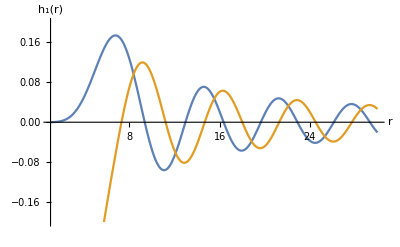

```mathematica
Plot[{Re@smslnn5[r],Im@smslnn5[r]},{r,1,30},AxesLabel->{"r","h_1(r)"},PlotRange->{Full,{-0.2,0.2}}]//SavePlot["scal-h1"]
```

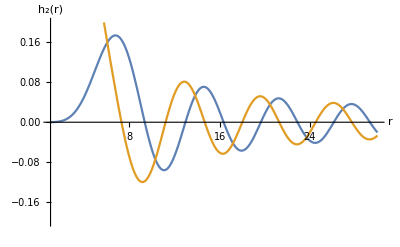

```mathematica
Plot[{Re@smslnnm5[r],Im@smslnnm5[r]},{r,1,30},AxesLabel->{"r","h_2(r)"},PlotRange->{Full,{-0.2,0.2}}]//SavePlot["scal-h2"]
```

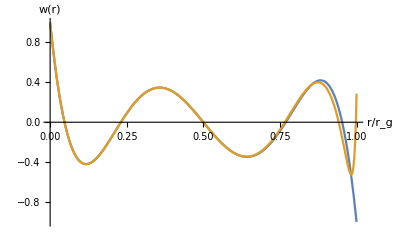

```mathematica
Plot[{Hypergeometric2F1[-5,6,1,r], ssln05},{r,0,1},AxesLabel->{"r/r_g","w(r)"}]//SavePlot["scal-r0-2f1-comp"]
```

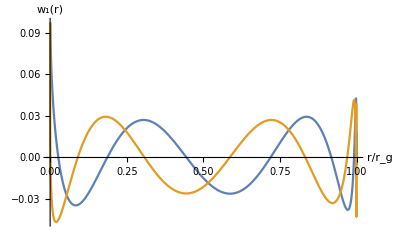

```mathematica
Plot[{Re@sslnn5[r],Im@sslnn5[r]},{r,0,1},AxesLabel->{"r/r_g","w_1(r)"}]//SavePlot["scal-rg-sec1"]
```

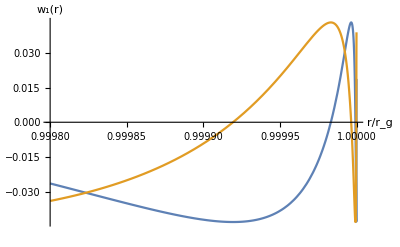

```mathematica
Plot[{Re@sslnn5[r],Im@sslnn5[r]},{r,1-0.0002,1},AxesLabel->{"r/r_g","w_1(r)"}]//SavePlot["scal-rg-sec1-rg"]
```

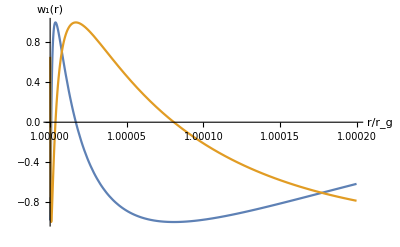

```mathematica
Plot[{Re@sslnn5[r],Im@sslnn5[r]},{r,1,1.0002},AxesLabel->{"r/r_g","w_1(r)"}]//SavePlot["scal-rg-sec2-rg"]
```

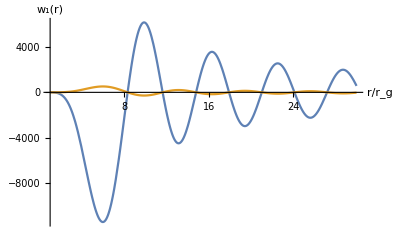

```mathematica
Plot[{Re@sslnn5[r],Im@sslnn5[r]},{r,1,30},AxesLabel->{"r/r_g","w_1(r)"},PlotRange->Full]//SavePlot["scal-rg-sec2"]
```

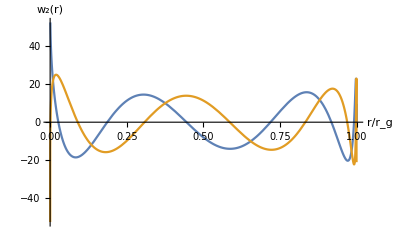

```mathematica
Plot[{Re@sslnnm5[r],Im@sslnnm5[r]},{r,0,1},AxesLabel->{"r/r_g","w_2(r)"}]//SavePlot["scal-rg2-sec1"]
```

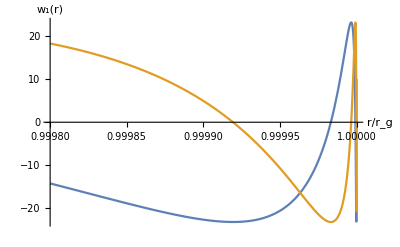

```mathematica
Plot[{Re@sslnnm5[r],Im@sslnnm5[r]},{r,1-0.0002,1},AxesLabel->{"r/r_g","w_1(r)"}]//SavePlot["scal-rg2-sec1-rg"]
```

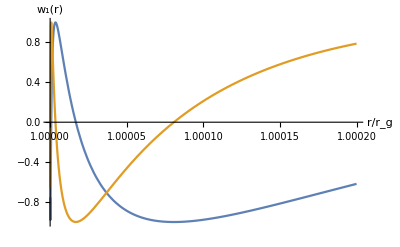

```mathematica
Plot[{Re@sslnnm5[r],Im@sslnnm5[r]},{r,1,1.0002},AxesLabel->{"r/r_g","w_1(r)"}]//SavePlot["scal-rg2-sec2-rg"]
```

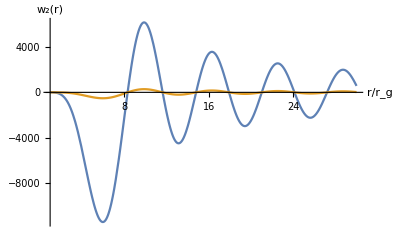

```mathematica
Plot[{Re@sslnnm5[r],Im@sslnnm5[r]},{r,1,30},AxesLabel->{"r/r_g","w_2(r)"},PlotRange->Full]//SavePlot["scal-rg2-sec2"]
```

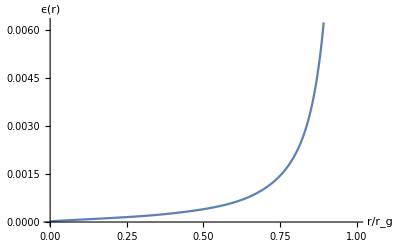

```mathematica
Plot[Re@seen5/.u->π/4//Evaluate,{r,0,1},AxesLabel->{"r/r_g","ϵ(r)"}]//SavePlot["scal-rg-ee-sec1"]
```

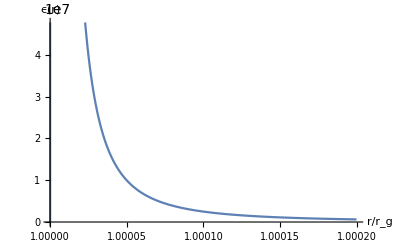

```mathematica
Plot[Re@seen5/.u->π/4//Evaluate,{r,1,1.0002},AxesLabel->{"r/r_g","ϵ(r)"}]//SavePlot["scal-rg-ee-sec2-rg"]
```

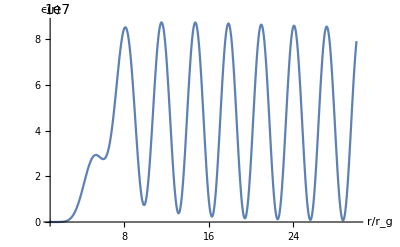

```mathematica
Plot[Re@seen5/.u->π/4//Evaluate,{r,1.0002,30},AxesLabel->{"r/r_g","ϵ(r)"}]//SavePlot["scal-rg-ee-sec2"]
```

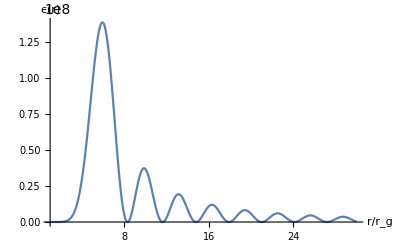

```mathematica
Plot[Re@seen5/.u->π/2//Evaluate,{r,1.0002,30},AxesLabel->{"r/r_g","ϵ(r)"},PlotRange->Full]//SavePlot["scal-rg-ee-sec2-p2"]
```

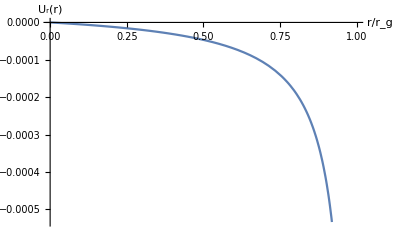

```mathematica
Plot[Re@sUUn5[[1]]/.u->π/4//Evaluate,{r,0,1},AxesLabel->{"r/r_g","U_r(r)"}]//SavePlot["scal-rg-uu-sec1"]
```

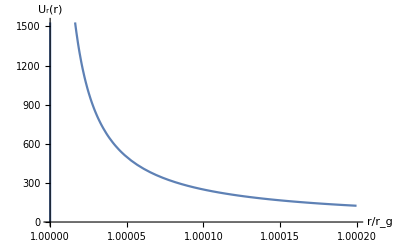

```mathematica
Plot[Re@sUUn5[[1]]/.u->π/4//Evaluate,{r,1,1.0002},AxesLabel->{"r/r_g","U_r(r)"}]//SavePlot["scal-rg-uu-sec2-rg"]
```

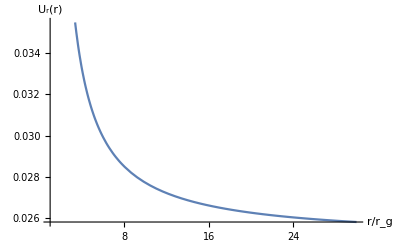

```mathematica
Plot[Re@sUUn5[[1]]/.u->π/4//Evaluate,{r,1.0002,30},AxesLabel->{"r/r_g","U_r(r)"}]//SavePlot["scal-rg-uu-sec2"]
```

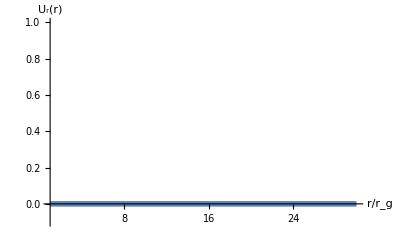

```mathematica
Plot[Re@sUUn5[[1]]/.u->π/2//Evaluate,{r,1.0002,30},AxesLabel->{"r/r_g","U_r(r)"},PlotStyle->{Thickness[0.01]}, PlotRange->{Full, {-0.1,1}}]//SavePlot["scal-rg-uu-sec2-p2"]
```

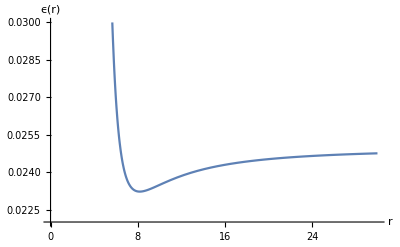

```mathematica
Plot[Re@smeen5/.u->π/4//Evaluate,{r,0,30},AxesLabel->{"r","ϵ(r)"},PlotRange->{Full, {0.022, 0.03}}]//SavePlot["scal-h1-ee"]
```

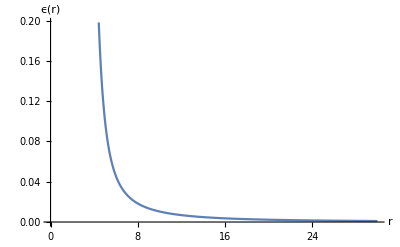

```mathematica
Plot[Re@smeen5/.u->π/2//Evaluate,{r,0,30},AxesLabel->{"r","ϵ(r)"}]//SavePlot["scal-h1-ee-p2"]
```

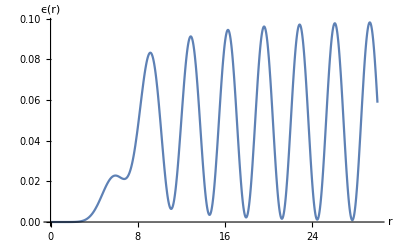

```mathematica
Plot[Re@smeens5/.u->π/4//Evaluate,{r,0,30},AxesLabel->{"r","ϵ(r)"}]//SavePlot["scal-j1-ee"]
```

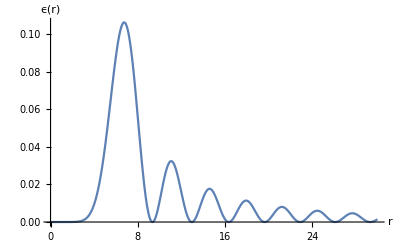

```mathematica
Plot[Re@smeens5/.u->π/2//Evaluate,{r,0,30},AxesLabel->{"r","ϵ(r)"},PlotRange->Full]//SavePlot["scal-j1-ee-p2"]
```

#### Векторное поле

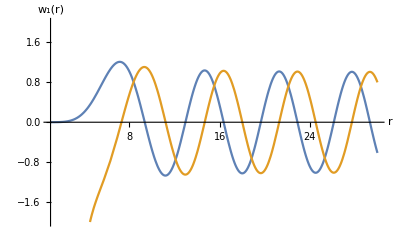

```mathematica
Plot[{Re@vmslnn5[r],Im@vmslnn5[r]},{r,1,30},AxesLabel->{"r","w_1(r)"}, PlotRange->{Full,{-2,2}}]//SavePlot["vec-h1"]
```

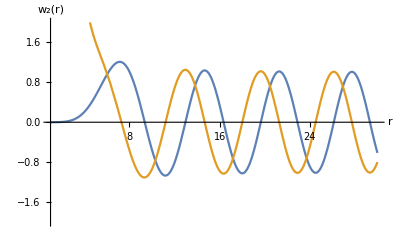

```mathematica
Plot[{Re@vmslnnm5[r],Im@vmslnnm5[r]},{r,1,30},AxesLabel->{"r","w_2(r)"}, PlotRange->{Full,{-2,2}}]//SavePlot["vec-h2"]
```

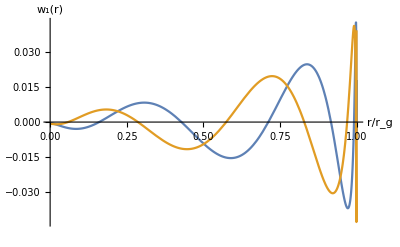

```mathematica
Plot[{Re@vslnn5[r],Im@vslnn5[r]},{r,0,1},AxesLabel->{"r/r_g","w_1(r)"}]//SavePlot["vec-rg-sec1"]
```

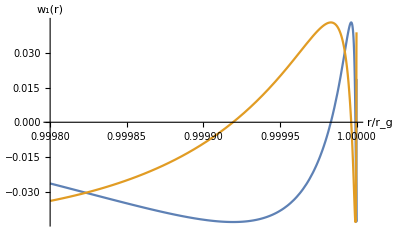

```mathematica
Plot[{Re@vslnn5[r],Im@vslnn5[r]},{r,1-0.0002,1},AxesLabel->{"r/r_g","w_1(r)"}]//SavePlot["vec-rg-sec1-rg"]
```

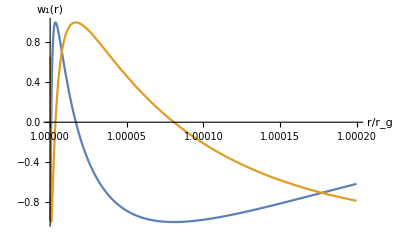

```mathematica
Plot[{Re@vslnn5[r],Im@vslnn5[r]},{r,1,1.0002},AxesLabel->{"r/r_g","w_1(r)"}]//SavePlot["vec-rg-sec2-rg"]
```

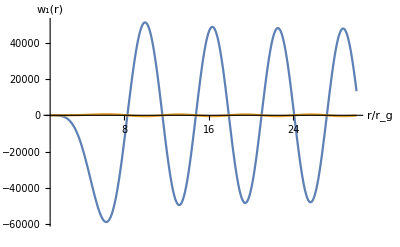

```mathematica
Plot[{Re@vslnn5[r],Im@vslnn5[r]},{r,1,30},AxesLabel->{"r/r_g","w_1(r)"},PlotRange->Full]//SavePlot["vec-rg-sec2"]
```

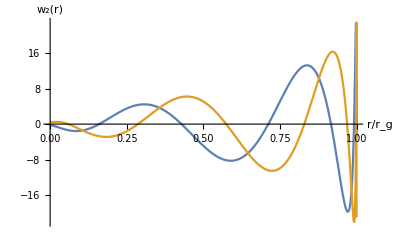

```mathematica
Plot[{Re@vslnnm5[r],Im@vslnnm5[r]},{r,0,1},AxesLabel->{"r/r_g","w_2(r)"}]//SavePlot["vec-rg2-sec1"]
```

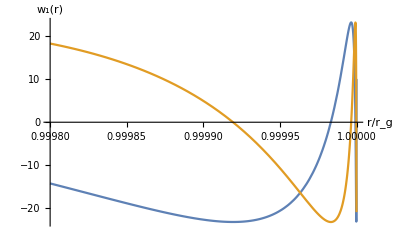

```mathematica
Plot[{Re@vslnnm5[r],Im@vslnnm5[r]},{r,1-0.0002,1},AxesLabel->{"r/r_g","w_1(r)"}]//SavePlot["vec-rg2-sec1-rg"]
```

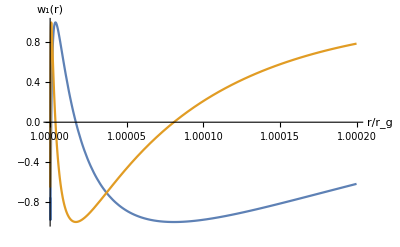

```mathematica
Plot[{Re@vslnnm5[r],Im@vslnnm5[r]},{r,1,1.0002},AxesLabel->{"r/r_g","w_1(r)"}]//SavePlot["vec-rg2-sec2-rg"]
```

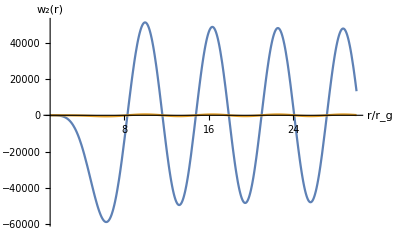

```mathematica
Plot[{Re@vslnnm5[r],Im@vslnnm5[r]},{r,1,30},AxesLabel->{"r/r_g","w_2(r)"},PlotRange->Full]//SavePlot["vec-rg2-sec2"]
```

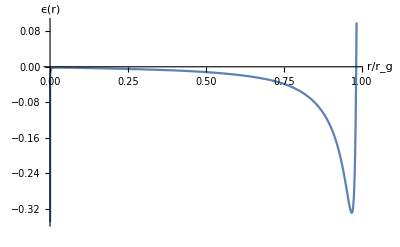

```mathematica
Plot[Re@veen5/.u->-π/4//Evaluate,{r,0,1},AxesLabel->{"r/r_g","ϵ(r)"},PlotRange->{All,{-0.35,0.1}}]//SavePlot["vec-rg-ee-sec1"]
```

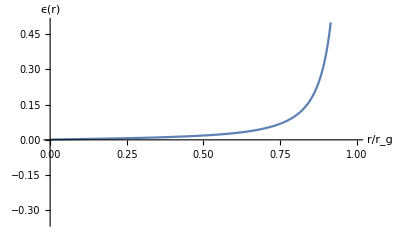

```mathematica
Plot[Re@veen5/.u->-π/2//Evaluate,{r,0,1},AxesLabel->{"r/r_g","ϵ(r)"},PlotRange->{Full,{-0.35,0.5}}]
```

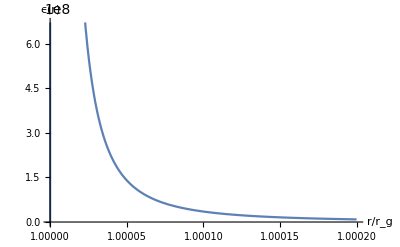

```mathematica
Quiet@Plot[Re@veen5/.u->-π/4//Evaluate,{r,1,1.0002},AxesLabel->{"r/r_g","ϵ(r)"}]//SavePlot["vec-rg-ee-sec2-rg"]
```

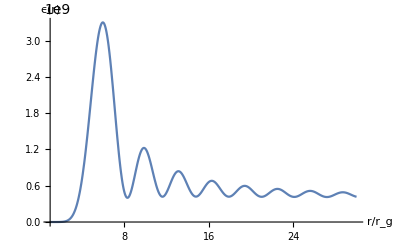

```mathematica
Plot[Re@veen5/.u->-π/4//Evaluate,{r,1.0002,30},AxesLabel->{"r/r_g","ϵ(r)"},PlotRange->Full]//SavePlot["vec-rg-ee-sec2"]
```

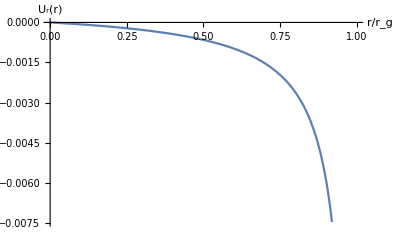

```mathematica
Plot[Re@vUUn5[[1]]/.u->-π/4//Evaluate,{r,0,1},AxesLabel->{"r/r_g","U_r(r)"}]//SavePlot["vec-rg-uu-sec1"]
```

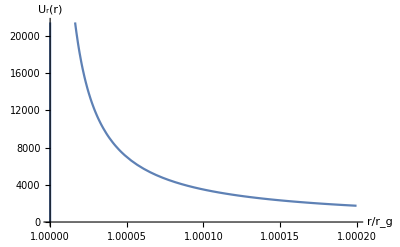

```mathematica
Plot[Re@vUUn5[[1]]/.u->-π/4//Evaluate,{r,1,1.0002},AxesLabel->{"r/r_g","U_r(r)"}]//SavePlot["vec-rg-uu-sec2-rg"]
```

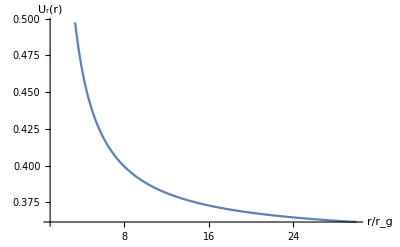

```mathematica
Plot[Re@vUUn5[[1]]/.u->-π/4//Evaluate,{r,1.0002,30},AxesLabel->{"r/r_g","U_r(r)"}]//SavePlot["vec-rg-uu-sec2"]
```

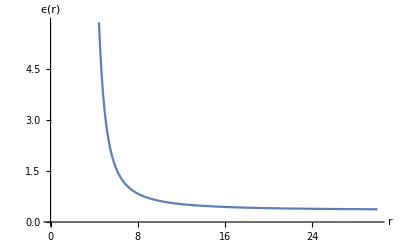

```mathematica
Plot[Re@vmeen5/.u->-π/4//Evaluate,{r,0,30},AxesLabel->{"r","ϵ(r)"}]//SavePlot["vec-h1-ee"]
```

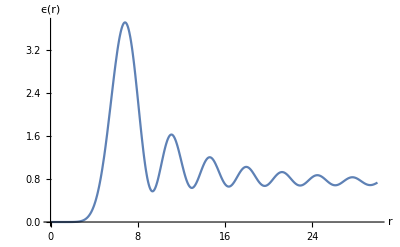

```mathematica
Plot[Re@vmeens5/.u->-π/4//Evaluate,{r,0,30},AxesLabel->{"r","ϵ(r)"},PlotRange->Full]//SavePlot["vec-j1-ee"]
```